```mathematica
goodgraph[graph_]:=Block[{vd=And@@Map[#>2&,VertexDegree[graph]]},Piecewise[{{Block[{vc=VertexConnectivity[graph]},Piecewise[{{Block[{ec=EdgeConnectivity[graph]},Piecewise[{{Block[{cyd=Length[FindCycle[graph,∞,3]]},Piecewise[{{True, cyd==3}, {False, cyd≠3}}]], ec>1}, {False, ec≤1}}]], vc>1}, {False, vc≤1}}]], vd}, {False, ¬vd}}]]
gedges[graph_]:=Block[{ged=(Length[EdgeList[graph]]≤15)},Piecewise[{{goodgraph[graph], ged}, {False, ¬ged}}]]
lt25= Select[GraphData[;;25],gedges[GraphData[#]]&];
Length[lt25]
```

176

```mathematica
hd[x1_,x2_]:=Block[{b1=IntegerDigits[x1,2],b2=IntegerDigits[x2,2]},
Block[{len=Max[Length[b1],Length[b2]]},
HammingDistance[PadLeft[b1,len],PadLeft[b2,len]]]]
```

```mathematica
Take[{1,2,3,4,5,6,7},2]
Drop[{1,2,3,4,5,6,7},3]
```

{1,2}

{4,5,6,7}

```mathematica
numcy[g_]:=Length[FindCycle[g,∞,All]]
```

```mathematica
flipnth[es_,len_,n_]:=Join[Take[es,n-1],{Last[es[[n]]]->First[es[[n]]]},Drop[es,n]]
alloneflips[{es_,len_}]:=Block[{(*es=EdgeList[g],len=EdgeCount[g],*)numcyg=numcy[Graph[es]]},
If[numcyg>0,Or@@Table[numcy[Graph[flipnth[es,len,i]]]<numcyg,{i,1,len}],True]]
```

```mathematica
alloneflips[Graph[{1->2,2->3,3->1}]]
```

True

```mathematica
numcy[Graph[{1->2,2->3,3->1}]]
```

1

```mathematica
nthorl[uelist_,n_,len_]:=
(*Block[{uelist=Map[{#[[1]],#[[2]]}&,EdgeList[graph]](*,len=EdgeCount[graph]*)},*)
Block[{blist=PadLeft[IntegerDigits[n,2],len]},
{Table[Piecewise[{{uelist[[i]][[1]]->uelist[[i]][[2]], blist[[i]]==0}, {uelist[[i]][[2]]->uelist[[i]][[1]], blist[[i]]==1}}],{i,1,len}],len}]
```

```mathematica
checkA[g_]:=Block[{len=EdgeCount[g],uelist=Map[{#[[1]],#[[2]]}&,EdgeList[g]]},And@@Table[alloneflips[nthorl[uelist,j,len]],{j,0,2^len}]]
```

```mathematica
checkA[CompleteGraph[4]]
```

True

```mathematica
Length[lt25]
```

176

```mathematica
ParallelTable[checkA[GraphData[lt25[[k]]]],{k,1,25}]
```

LinkObject::linkd: Unable to communicate with closed link LinkObject["'/Applications/Mathematica.app/Contents/MacOS/WolframKernel' -subkernel -noinit -wstp", 2139, 10].

Kernels::rdead: Subkernel connected through "KernelObject"[6, "local"] appears dead.

Parallel`Developer`QueueRun::req: Requeueing evaluations {40} assigned to "KernelObject"[6, "local", "<defunct>"].

LinkObject::linkd: Unable to communicate with closed link LinkObject["'/Applications/Mathematica.app/Contents/MacOS/WolframKernel' -subkernel -noinit -wstp", 2137, 8].

Kernels::rdead: Subkernel connected through "KernelObject"[4, "local"] appears dead.

Parallel`Developer`QueueRun::req: Requeueing evaluations {41} assigned to "KernelObject"[4, "local", "<defunct>"].

LinkObject::linkd: Unable to communicate with closed link LinkObject["'/Applications/Mathematica.app/Contents/MacOS/WolframKernel' -subkernel -noinit -wstp", 2135, 6].

General::stop: Further output of LinkObject :: linkd will be suppressed during this calculation.

Kernels::rdead: Subkernel connected through "KernelObject"[2, "local"] appears dead.

General::stop: Further output of Kernels :: rdead will be suppressed during this calculation.

Parallel`Developer`QueueRun::req: Requeueing evaluations {42} assigned to "KernelObject"[2, "local", "<defunct>"].

General::stop: Further output of Parallel`Developer`QueueRun :: req will be suppressed during this calculation.

LaunchKernels::clone: Kernel "KernelObject"[6, "local", "<defunct>"] resurrected as "KernelObject"[10, "local"].

LaunchKernels::clone: Kernel "KernelObject"[4, "local", "<defunct>"] resurrected as "KernelObject"[11, "local"].

LaunchKernels::clone: Kernel "KernelObject"[2, "local", "<defunct>"] resurrected as "KernelObject"[12, "local"].

General::stop: Further output of LaunchKernels :: clone will be suppressed during this calculation.

Initializing GraphData indices ....

Initializing GraphData indices ....

Initializing GraphData indices ....

«15 more identical outputs»

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

```mathematica
ParallelTable[checkA[GraphData[lt25[[k]]]],{k,26,50}]
```

LinkObject::linkd: Unable to communicate with closed link LinkObject["'/Applications/Mathematica.app/Contents/MacOS/WolframKernel' -subkernel -noinit -wstp", 2490, 8].

Kernels::rdead: Subkernel connected through "KernelObject"[11, "local"] appears dead.

Parallel`Developer`QueueRun::req: Requeueing evaluations {50} assigned to "KernelObject"[11, "local", "<defunct>"].

LinkObject::linkd: Unable to communicate with closed link LinkObject["'/Applications/Mathematica.app/Contents/MacOS/WolframKernel' -subkernel -noinit -wstp", 2427, 9].

Kernels::rdead: Subkernel connected through "KernelObject"[9, "local"] appears dead.

Parallel`Developer`QueueRun::req: Requeueing evaluations {52} assigned to "KernelObject"[9, "local", "<defunct>"].

LinkObject::linkd: Unable to communicate with closed link LinkObject["'/Applications/Mathematica.app/Contents/MacOS/WolframKernel' -subkernel -noinit -wstp", 2422, 7].

General::stop: Further output of LinkObject :: linkd will be suppressed during this calculation.

Kernels::rdead: Subkernel connected through "KernelObject"[8, "local"] appears dead.

General::stop: Further output of Kernels :: rdead will be suppressed during this calculation.

Parallel`Developer`QueueRun::req: Requeueing evaluations {53} assigned to "KernelObject"[8, "local", "<defunct>"].

General::stop: Further output of Parallel`Developer`QueueRun :: req will be suppressed during this calculation.

LaunchKernels::clone: Kernel "KernelObject"[11, "local", "<defunct>"] resurrected as "KernelObject"[13, "local"].

LaunchKernels::clone: Kernel "KernelObject"[9, "local", "<defunct>"] resurrected as "KernelObject"[14, "local"].

LaunchKernels::clone: Kernel "KernelObject"[8, "local", "<defunct>"] resurrected as "KernelObject"[15, "local"].

General::stop: Further output of LaunchKernels :: clone will be suppressed during this calculation.

Initializing GraphData indices ....

Initializing GraphData indices ....

Initializing GraphData indices ....

«9 more identical outputs»

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

```mathematica
ParallelTable[checkA[GraphData[lt25[[k]]]],{k,51,75}]
```

LinkObject::linkd: Unable to communicate with closed link LinkObject["'/Applications/Mathematica.app/Contents/MacOS/WolframKernel' -subkernel -noinit -wstp", 2568, 9].

Kernels::rdead: Subkernel connected through "KernelObject"[16, "local"] appears dead.

Parallel`Developer`QueueRun::req: Requeueing evaluations {61} assigned to "KernelObject"[16, "local", "<defunct>"].

LinkObject::linkd: Unable to communicate with closed link LinkObject["'/Applications/Mathematica.app/Contents/MacOS/WolframKernel' -subkernel -noinit -wstp", 2560, 8].

Kernels::rdead: Subkernel connected through "KernelObject"[15, "local"] appears dead.

Parallel`Developer`QueueRun::req: Requeueing evaluations {62} assigned to "KernelObject"[15, "local", "<defunct>"].

LinkObject::linkd: Unable to communicate with closed link LinkObject["'/Applications/Mathematica.app/Contents/MacOS/WolframKernel' -subkernel -noinit -wstp", 2555, 7].

General::stop: Further output of LinkObject :: linkd will be suppressed during this calculation.

Kernels::rdead: Subkernel connected through "KernelObject"[14, "local"] appears dead.

General::stop: Further output of Kernels :: rdead will be suppressed during this calculation.

Parallel`Developer`QueueRun::req: Requeueing evaluations {63} assigned to "KernelObject"[14, "local", "<defunct>"].

General::stop: Further output of Parallel`Developer`QueueRun :: req will be suppressed during this calculation.

LaunchKernels::clone: Kernel "KernelObject"[16, "local", "<defunct>"] resurrected as "KernelObject"[17, "local"].

LaunchKernels::clone: Kernel "KernelObject"[15, "local", "<defunct>"] resurrected as "KernelObject"[18, "local"].

LaunchKernels::clone: Kernel "KernelObject"[14, "local", "<defunct>"] resurrected as "KernelObject"[19, "local"].

General::stop: Further output of LaunchKernels :: clone will be suppressed during this calculation.

Initializing GraphData indices ....

Initializing GraphData indices ....

Initializing GraphData indices ....

«15 more identical outputs»

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

```mathematica
ParallelTable[checkA[GraphData[lt25[[k]]]],{k,76,100}]
```

LinkObject::linkd: Unable to communicate with closed link LinkObject["'/Applications/Mathematica.app/Contents/MacOS/WolframKernel' -subkernel -noinit -wstp", 2636, 10].

Kernels::rdead: Subkernel connected through "KernelObject"[22, "local"] appears dead.

Parallel`Developer`QueueRun::req: Requeueing evaluations {73} assigned to "KernelObject"[22, "local", "<defunct>"].

LinkObject::linkd: Unable to communicate with closed link LinkObject["'/Applications/Mathematica.app/Contents/MacOS/WolframKernel' -subkernel -noinit -wstp", 2635, 9].

Kernels::rdead: Subkernel connected through "KernelObject"[21, "local"] appears dead.

Parallel`Developer`QueueRun::req: Requeueing evaluations {74} assigned to "KernelObject"[21, "local", "<defunct>"].

LinkObject::linkd: Unable to communicate with closed link LinkObject["'/Applications/Mathematica.app/Contents/MacOS/WolframKernel' -subkernel -noinit -wstp", 2634, 8].

General::stop: Further output of LinkObject :: linkd will be suppressed during this calculation.

Kernels::rdead: Subkernel connected through "KernelObject"[20, "local"] appears dead.

General::stop: Further output of Kernels :: rdead will be suppressed during this calculation.

Parallel`Developer`QueueRun::req: Requeueing evaluations {75} assigned to "KernelObject"[20, "local", "<defunct>"].

General::stop: Further output of Parallel`Developer`QueueRun :: req will be suppressed during this calculation.

LaunchKernels::clone: Kernel "KernelObject"[22, "local", "<defunct>"] resurrected as "KernelObject"[23, "local"].

LaunchKernels::clone: Kernel "KernelObject"[21, "local", "<defunct>"] resurrected as "KernelObject"[24, "local"].

LaunchKernels::clone: Kernel "KernelObject"[20, "local", "<defunct>"] resurrected as "KernelObject"[25, "local"].

General::stop: Further output of LaunchKernels :: clone will be suppressed during this calculation.

Initializing GraphData indices ....

Initializing GraphData indices ....

Initializing GraphData indices ....

«15 more identical outputs»

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

```mathematica
Timing[ParallelTable[checkA[GraphData[lt25[[k]]]],{k,101,125}]]
```

LinkObject::linkd: Unable to communicate with closed link LinkObject["'/Applications/Mathematica.app/Contents/MacOS/WolframKernel' -subkernel -noinit -wstp", 2704, 10].

Kernels::rdead: Subkernel connected through "KernelObject"[28, "local"] appears dead.

Parallel`Developer`QueueRun::req: Requeueing evaluations {85} assigned to "KernelObject"[28, "local", "<defunct>"].

LinkObject::linkd: Unable to communicate with closed link LinkObject["'/Applications/Mathematica.app/Contents/MacOS/WolframKernel' -subkernel -noinit -wstp", 2703, 9].

Kernels::rdead: Subkernel connected through "KernelObject"[27, "local"] appears dead.

Parallel`Developer`QueueRun::req: Requeueing evaluations {86} assigned to "KernelObject"[27, "local", "<defunct>"].

LinkObject::linkd: Unable to communicate with closed link LinkObject["'/Applications/Mathematica.app/Contents/MacOS/WolframKernel' -subkernel -noinit -wstp", 2702, 8].

General::stop: Further output of LinkObject :: linkd will be suppressed during this calculation.

Kernels::rdead: Subkernel connected through "KernelObject"[26, "local"] appears dead.

General::stop: Further output of Kernels :: rdead will be suppressed during this calculation.

Parallel`Developer`QueueRun::req: Requeueing evaluations {87} assigned to "KernelObject"[26, "local", "<defunct>"].

General::stop: Further output of Parallel`Developer`QueueRun :: req will be suppressed during this calculation.

LaunchKernels::clone: Kernel "KernelObject"[28, "local", "<defunct>"] resurrected as "KernelObject"[29, "local"].

LaunchKernels::clone: Kernel "KernelObject"[27, "local", "<defunct>"] resurrected as "KernelObject"[30, "local"].

LaunchKernels::clone: Kernel "KernelObject"[26, "local", "<defunct>"] resurrected as "KernelObject"[31, "local"].

General::stop: Further output of LaunchKernels :: clone will be suppressed during this calculation.

Initializing GraphData indices ....

Initializing GraphData indices ....

Initializing GraphData indices ....

«15 more identical outputs»

{27.5808,{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}}

```mathematica
Timing[ParallelTable[checkA[GraphData[lt25[[k]]]],{k,126,150}]]
```

LinkObject::linkd: Unable to communicate with closed link LinkObject["'/Applications/Mathematica.app/Contents/MacOS/WolframKernel' -subkernel -noinit -wstp", 2772, 10].

Kernels::rdead: Subkernel connected through "KernelObject"[34, "local"] appears dead.

Parallel`Developer`QueueRun::req: Requeueing evaluations {97} assigned to "KernelObject"[34, "local", "<defunct>"].

LinkObject::linkd: Unable to communicate with closed link LinkObject["'/Applications/Mathematica.app/Contents/MacOS/WolframKernel' -subkernel -noinit -wstp", 2770, 8].

Kernels::rdead: Subkernel connected through "KernelObject"[32, "local"] appears dead.

Parallel`Developer`QueueRun::req: Requeueing evaluations {99} assigned to "KernelObject"[32, "local", "<defunct>"].

LinkObject::linkd: Unable to communicate with closed link LinkObject["'/Applications/Mathematica.app/Contents/MacOS/WolframKernel' -subkernel -noinit -wstp", 2762, 7].

General::stop: Further output of LinkObject :: linkd will be suppressed during this calculation.

Kernels::rdead: Subkernel connected through "KernelObject"[31, "local"] appears dead.

General::stop: Further output of Kernels :: rdead will be suppressed during this calculation.

Parallel`Developer`QueueRun::req: Requeueing evaluations {100} assigned to "KernelObject"[31, "local", "<defunct>"].

General::stop: Further output of Parallel`Developer`QueueRun :: req will be suppressed during this calculation.

LaunchKernels::clone: Kernel "KernelObject"[34, "local", "<defunct>"] resurrected as "KernelObject"[35, "local"].

LaunchKernels::clone: Kernel "KernelObject"[32, "local", "<defunct>"] resurrected as "KernelObject"[36, "local"].

LaunchKernels::clone: Kernel "KernelObject"[31, "local", "<defunct>"] resurrected as "KernelObject"[37, "local"].

General::stop: Further output of LaunchKernels :: clone will be suppressed during this calculation.

Initializing GraphData indices ....

Initializing GraphData indices ....

Initializing GraphData indices ....

«12 more identical outputs»

{40.2965,{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}}

```mathematica
Timing[ParallelTable[checkA[GraphData[lt25[[k]]]],{k,151,176}]]
```

LinkObject::linkd: Unable to communicate with closed link LinkObject["'/Applications/Mathematica.app/Contents/MacOS/WolframKernel' -subkernel -noinit -wstp", 2839, 10].

Kernels::rdead: Subkernel connected through "KernelObject"[39, "local"] appears dead.

Parallel`Developer`QueueRun::req: Requeueing evaluations {109} assigned to "KernelObject"[39, "local", "<defunct>"].

LinkObject::linkd: Unable to communicate with closed link LinkObject["'/Applications/Mathematica.app/Contents/MacOS/WolframKernel' -subkernel -noinit -wstp", 2830, 7].

Kernels::rdead: Subkernel connected through "KernelObject"[37, "local"] appears dead.

Parallel`Developer`QueueRun::req: Requeueing evaluations {111} assigned to "KernelObject"[37, "local", "<defunct>"].

LinkObject::linkd: Unable to communicate with closed link LinkObject["'/Applications/Mathematica.app/Contents/MacOS/WolframKernel' -subkernel -noinit -wstp", 2820, 5].

General::stop: Further output of LinkObject :: linkd will be suppressed during this calculation.

Kernels::rdead: Subkernel connected through "KernelObject"[35, "local"] appears dead.

General::stop: Further output of Kernels :: rdead will be suppressed during this calculation.

Parallel`Developer`QueueRun::req: Requeueing evaluations {113} assigned to "KernelObject"[35, "local", "<defunct>"].

General::stop: Further output of Parallel`Developer`QueueRun :: req will be suppressed during this calculation.

LaunchKernels::clone: Kernel "KernelObject"[39, "local", "<defunct>"] resurrected as "KernelObject"[40, "local"].

LaunchKernels::clone: Kernel "KernelObject"[37, "local", "<defunct>"] resurrected as "KernelObject"[41, "local"].

LaunchKernels::clone: Kernel "KernelObject"[35, "local", "<defunct>"] resurrected as "KernelObject"[42, "local"].

General::stop: Further output of LaunchKernels :: clone will be suppressed during this calculation.

Initializing GraphData indices ....

Initializing GraphData indices ....

Initializing GraphData indices ....

«9 more identical outputs»

{24.9147,{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}}

```mathematica
FindCycle[CompleteGraph[4],∞,All]
counttrivup[CompleteGraph[4],First[%]]
counttrivup[g_,cy_]:=Length[cy]*2^(EdgeCount[Subgraph[g,Complement[VertexList[g],Sort[Map[First,cy]]]]])
alltrivup[g_]:=Sum[counttrivup[g,cy],{cy,FindCycle[g,∞,All]}]
```

{{2<->3,3<->4,4<->2},{1<->4,4<->2,2<->1},{1<->2,2<->3,3<->1},{1<->4,4<->3,3<->1},{1<->4,4<->3,3<->2,2<->1},{1<->2,2<->4,4<->3,3<->1},{1<->4,4<->2,2<->3,3<->1}}

3

```mathematica
alltrivup[CompleteGraph[3]]
```

3

```mathematica
alltrivup[CompleteGraph[4]]
```

24

```mathematica
alltrivup[CompleteGraph[5]]
```

180

```mathematica
alltrivup[CompleteGraph[6]]
```

1560

```mathematica
alltrivup[CompleteGraph[7]]
```

17640

```mathematica
alltrivup[CompleteGraph[8]]
```

313152

```mathematica
2^EdgeCount[CompleteGraph[3]]
```

```mathematica
3/8
```

```mathematica
2^EdgeCount[CompleteGraph[4]]
```

```mathematica
24/64
```

```mathematica
2^EdgeCount[CompleteGraph[5]]
```

```mathematica
180/1024
```

```mathematica
2^EdgeCount[CompleteGraph[6]]
```

```mathematica
1560/32768
```

```mathematica
2^EdgeCount[CompleteGraph[7]]
```

```mathematica
17640/2097152
```

```mathematica
2^EdgeCount[CompleteGraph[8]]
```

```mathematica
313152/268435456
```

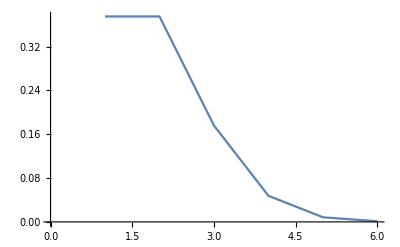

```mathematica
ListPlot[N[{3/8,24/64,180/1024,1560/32768,17640/2097152,313152/268435456}],Joined->True]
```

```mathematica
numcy[CompleteGraph[3]]
```

1

```mathematica
numcy[CompleteGraph[4]]
```

7

```mathematica
numcy[CompleteGraph[5]]
```

37

```mathematica
ϵi≥2
```

```mathematica
ϵ1+1+nPs[v1->v1'&e0]≤nPs[v1'->v1&e0]

ϕ1≥3
ϕ1+nPs[v1->v1'&e0]==nPs[v1'->v1&e0]

nPs[e0]≥3


nPs[v2->v2'&!e0&!e1]==nPs[v2'->v2&!e0&!e1]+ϵ2

nPs[v2->v2'&!e1]==nPs[v2->v2'&!e0&!e1]+nPs[v2->v2'&e0&!e1]≥ϵ2+ϕ1≥5
nPs[v2'->v2&!e1]==nPs[v2'->v2&!e0&!e1]+nPs[v2'->v2&e0&!e1]

nPs[v0'->v0]≥ϵ2+ϕ1+ϵ1≥7
```

```mathematica
Reduce[{a-δ0==b c+d1,b-1==a c+d2,c-1==b c+d3,a≥1,b≥1,c≥1,δ0≥2,d1≥0,d2≥0,d3≥0},Integers]
```

```mathematica
Reduce[{a+2==b c+d1,b+1==a c+d2,c+1==a b+d3,a≥1,b≥1,c≥1,δ0≥2,d1≥0,d2≥0,d3≥0},Integers]
```

δ0∈Integers&&δ0≥2&&d1==2+a-b c&&d2==1+b-a c&&d3==1-a b+c&&((a==1&&b==1&&c==1)||(a==1&&b==1&&c==2)||(a==1&&b==2&&c==1)||(a==2&&b==1&&c==1))

```mathematica
Reduce[{a-2==b c+d1,b-1==a c+d2,c-1==a b+d3,a≥1,b≥1,c≥1,δ0≥2,d1==0,d2==0,d3==0},Integers]
```

False

```mathematica
Reduce[{a-2≥b+d1,b-1≥c+d2,c-1≥a+d3,a≥1,b≥1,c≥1,δ0≥2,d1==0,d2==0,d3==0},Integers]
```

False

```mathematica
Reduce[{a-2==b c+d1,b-1==a c+d2,c-1==a b+d3,a≥1,b≥1,c≥1,δ0≥2,d1≥0,d2≥0,d3≥0},Integers]
```

False

```mathematica
Simplify[LogicalExpand[Reduce[{a-δ0==b c+d1,b-δ1==a c+d2,c-δ2==a b+d3,a≥1,b≥1,c≥1,δ0≥1,d1≥0,d2≥0,d3≥0},Integers]],{(a|b|c|d1|d2|d3|δ0|δ1|δ2)∈Integers,a≥1,b≥1,c≥1,d1≥0,d2≥0,d3≥0,δ0≥1}]
```

(a==1+b c&&d1==0&&δ0==1&&b==c+b c^2+d2+δ1&&b+b^2 c+d3+δ2==c&&c+b c^2+δ1≤b)||(b^2 c+d3+b (d1+δ0)+δ2==c&&b^2+c (-c+d3+δ2)==b (d2+δ1)&&a b+d3+δ2==c&&b+b^2 c+d3+δ2<c&&b^2 c+d3+b δ0+δ2≤c&&c^2+b δ1≤b^2+c (d3+δ2))

```mathematica
LogicalExpand[Simplify[Reduce[{a-δ0==b c+d1,b-δ1==a c+d2,c-δ2==a b+d3,a≥1,b≥1,c≥1,d1≥0,d2≥0,d3≥0,δ0≥2},{δ0,δ1,δ2},Integers],{(a|b|c|d1|d2|d3|δ0|δ1|δ2)∈Integers,a≥1,b≥1,c≥1,d1≥0,d2≥0,d3≥0,δ0≥2}]]
```

(b==1&&c==1&&3+d1==a&&δ0==2&&2+d1+d2+δ1==0&&2+d1+d3+δ2==0)||(b==1&&2+c+d1==a&&δ0==2&&a^2+d2+δ1==1+a (2+d1)&&2+d1+d3+δ2==0&&a>3+d1)||(b c+d1+δ0==a&&a c+d2+δ1==b&&a b+d3+δ2==c&&a>3+d1&&a>2+c+d1&&2+b c+d1≤a)

```mathematica
a-2==b c+d1
b-1==a c+d2
c-1==a b+d3
```

```mathematica
a-f1==b c+d1
b-f2==a c+d2
c-f3==a b+d3
{d1,d2,d3}≥0
{a,b,c}≥1

a-f1-d1==b c≥b==a c+f2+d2≥a+f2+d2
a-f1-d1≥a+f2+d2
-f1-d1-d2≥+f2
-2≥-(f1+d1+d2)≥f2
-2≥f2≥1
```

```mathematica
Reduce[-2≥f2≥1]
```

False

```mathematica
Reduce[{a≥a c+f1+d1+f2+d2,a≥1,c≥1,d1≥0,d2≥0},Integers]
```

(a|c|d1|d2|f1|f2)∈Integers&&d2≥0&&d1≥0&&c≥1&&a≥1&&f1≤a-a c-d1-d2-f2

```mathematica
Expand[(a c+d2+f2)(a b+d3+f3)]
```

```mathematica
Factor[a^2 b c+a b d2+a c d3+d2 d3+a b f2+d3 f2+a c f3+d2 f3+f2 f3]
```

```mathematica
Reduce[{a b≥b,a≥1,b≥1}]
```

b≥1&&a≥1

```mathematica
Simplify[Reduce[{a≥b≥1,c≥d≥1,a c≥b d},Integers],{(a|b|c|d)∈Integers,c≥d,b≥1,d≥1,a≥b}]
```

True

```mathematica
Drop[{1,2,3,4,5},{4}]
```

{1,2,3,5}

```mathematica
xvarstr[i_]:=StringJoin["x",ToString[i]]
dvarstr[i_]:=StringJoin["d",ToString[i]]
(*jthprod[j_]:=Drop[prod,{j+1}]*)

forms[n_]:=Block[{prod=Join[Table[StringJoin[xvarstr[i],"*"],{i,0,n-1}],{"1"}]},Module[{form:=Join[{xvarstr[#]},{"=="},Drop[prod,{#}+1],{"+"},{dvarstr[#]}]&},

ToExpression[StringJoin["Exists[",ToString[Map[ToExpression,Join[Table[xvarstr[i],{i,0,n-1}],Table[dvarstr[i],{i,0,n-1}]]]],",",
ToString[Fold[#1&&#2&,Join[Table[ToExpression[StringJoin[form[j]]],{j,0,n-1}],Table[ToExpression[StringJoin[dvarstr[i],"≥1"]],{i,0,n-1}],Table[ToExpression[StringJoin[xvarstr[i],"≥1"]],{i,0,n-1}],Table[ToExpression[StringJoin["Element[",xvarstr[i],",Integers]"]],{i,0,n-1}],
Table[ToExpression[StringJoin["Element[",dvarstr[i],",Integers]"]],{i,0,n-1}]]]],"]"]]]]
Reduce[forms[3]]
```

False

```mathematica
Timing[Resolve[Timing[forms[2]]]]
```

{0.002193,False}

```mathematica
Timing[Reduce[forms[2]]]
```

{0.009765,False}

```mathematica
Timing[Resolve[forms[3]]]
```

{0.14385,False}

```mathematica
Timing[Reduce[forms[3]]]
```

{0.138331,False}

```mathematica
Timing[Resolve[forms[4]]]
```

{0.431082,False}

```mathematica
Timing[Reduce[forms[4]]]
```

{0.453137,False}

```mathematica
Timing[Resolve[forms[5]]]
```

$Aborted

```mathematica
Timing[Reduce[forms[6]]]
```

```mathematica
Timing[forms[2]]
```

{0.007069,C[1]∈Integers&&C[1]≥0&&d0==0&&d1==0&&x0==1+C[1]&&x1==1+C[1]}

```mathematica
Timing[forms[3]]
```

{6.99434,d0==0&&d1==0&&d2==0&&x0==1&&x1==1&&x2==1}

```mathematica
Timing[forms[4]]
```

$Aborted

```mathematica
Timing[forms[5]]
```

```mathematica
Timing[forms[6]]
```

```mathematica
x=p.xi+d
d≥0
x≥1
```

```mathematica
Reduce[{{x1,x2,x3}=={1,1,1}*(x1*x2*x3)*{1/x1,1/x2,1/x3}+{d1,d2,d3},{x1,x2,x3}>0,{d1,d2,d3}≥0},Integers]
```

d1==0&&d2==0&&d3==0&&x1==1&&x2==1&&x3==1

```mathematica
a+δ1==b c+d1
b+δ2==a c+d2
c+δ3==a b+d3

a==b==c
δ1==a^2-a+d1
δ2==a^2-a+d2
δ3==a^2-a+d3

δ1==a(a-1)+d1≥1
δ2==a(a-1)+d2≥1
δ3==a(a-1)+d3≥1

a(a-1)+di≥1
```

```mathematica
Reduce[{a+δ1==b c+d1,b+δ2==a c+d2,c+δ3==a b+d3,a≥1,b≥1,c≥1,d1≥0,d2≥0,d3≥0,δ1≥1,δ2≥1,δ3≥1},Integers]
```

```mathematica
Resolve[ForAll[a,a∈A&&Exists[b,b∈B&&b⊆a]]]
```

Resolve::elemc: Unable to resolve the domain or region membership condition a ∈ A.

```mathematica
Resolve[∀_a(a∈A&&∃_b(b∈B&&b⊆a))]⇒[B]<[A]
```

```mathematica
[A]≤[B]
∀_a(a∈A&&∃_b(b∈B&&b⊆a))
```

```mathematica
δ[i]≥1
ϵ[i]≥0
x[i]-δ[i]≥x[i+1]+ϵ[i]
```

```mathematica
x1-d1≥x2+e1
x2-d2≥x3+e2
x3-d3≥x1+e3
x1≥1
x2≥1
x3≥1
d1≥1
d2≥1
d3≥1
e1≥0
e2≥0
e3≥0
"→";
x1-d1≥x2
x2-d2≥x3
x3-d3≥x1
"→";
x1≥x2+d1
x2≥x3+d2
x3≥x1+d3
```

```mathematica
Reduce[{x1≥x2+d1,x2≥x3+d2,x3≥x1+d3,x1≥1,x2≥1,x3≥1,d1≥1,d2≥1,d3≥1},Integers]
```

False

```mathematica
x1≥x2+d1≥x3+d2+d1≥x1+d3+d2+d1
x2≥x3+d2
x3≥x1+d3

x1≥x1+d3+d2+d1
0≥d3+d2+d1
```

```mathematica
m=5;
Table[ToExpression[StringJoin["x",ToString[i]]],{i,0,m}]
```

```mathematica
Clear[m]
```

```mathematica
ser[m_]:=Normal[Last[CoefficientArrays[lastdiff[Table[ToExpression[StringJoin["x",ToString[i]]],{i,0,m}]]]]]
```

```mathematica
difs[l_]:=Table[l[[i+1]]-l[[i]],{i,1,Length[l]-1}]
```

```mathematica
lastdiff[l_]:=First[Nest[difs,l,Length[l]-1]]
```

```mathematica
Table[ser[j],{j,1,9}]//Column
```

{-1,1}
{1,-2,1}
{-1,3,-3,1}
{1,-4,6,-4,1}
{-1,5,-10,10,-5,1}
{1,-6,15,-20,15,-6,1}
{-1,7,-21,35,-35,21,-7,1}
{1,-8,28,-56,70,-56,28,-8,1}
{-1,9,-36,84,-126,126,-84,36,-9,1}

```mathematica
FindVertexIndependentPaths
```

```mathematica
nthor[graph_,n_]:=
Graph[Block[{uelist=Map[{#[[1]],#[[2]]}&,EdgeList[graph]],len=EdgeCount[graph]},
Block[{blist=PadLeft[IntegerDigits[n,2],len]},
Table[Piecewise[{{uelist[[i]][[1]]->uelist[[i]][[2]], blist[[i]]==0}, {uelist[[i]][[2]]->uelist[[i]][[1]], blist[[i]]==1}}],{i,1,len}]]]]
```

```mathematica
nthor[CompleteGraph[4],1]
```

```mathematica
FindVertexIndependentPaths[-Graphics-,1,2,∞]
```

{{1,2}}

```mathematica
checkL[g_]:=
```

```mathematica
subpQ[list_,a_,b_]:=Block[{pa=Flatten[Position[list,a]],pb=Flatten[Position[list,b]]},If[Length[pa]>0,If[Length[pb]>0,First[pa]<First[pb],False],False]]
```

```mathematica
checkLAux[g_,e_,v0_,v3_]:=
(*Block[{e=EdgeList[g][[i]]},*)
Block[{v1=First[e],v2=Last[e]},
If[Length[DeleteDuplicates[{v0,v1,v2,v3}]]==4,
If[Length[FindCycle[g]]≠0,
Block[{aps=FindVertexIndependentPaths[g,v0,v3,∞]},
Block[{ps0=Select[aps,subpQ[#,v1,v2]&]},
If[Length[ps0]>0,
Block[{ps1=FindVertexIndependentPaths[g,v0,v1,∞]},
Block[{vsPs1=Sort[DeleteDuplicates[Flatten[ps1]]]},
Block[{ps2=Select[FindVertexIndependentPaths[g,v2,v3,∞],Length[Intersection[vsPs1,#]]==0&]},
If[Length[ps2]>0,Length[aps]>Length[ps1],True]]]]
,True]]],True],True]]
```

```mathematica
checkL[g_]:=Select[Flatten[Block[{vs=VertexList[g],es=EdgeList[g]},Table[{e,v0,v3,checkLAux[g,e,v0,v3]},{e,es},{v0,vs},{v3,vs}]],2],Last[#]==False&]
```

```mathematica
checkL[nthor[CompleteGraph[4],1]]
```

{}

```mathematica
"If #Ps(v0->v3 && v0->v1)>0, e1=(v1,v2), and P(v2->v3 and not incl. any vertices in Ps(), 
then #Ps(v0->v3)≥#Ps(v0->v1)";
```

```mathematica
EdgeCount[CompleteGraph[4]]
```

6

```mathematica
Select[Table[Block[{or=nthor[CompleteGraph[4],j]},{j,Length[FindCycle[or,∞,All]],VertexConnectivity[or],checkL[or]}],{j,0,2^6-1}],Length[Last[#]]≠0&]//Column
```

{8,3,1,{{4->1,3,2,False}}}
{10,3,1,{{3->4,2,1,False}}}
{12,3,1,{{4->1,2,3,False}}}
{13,3,1,{{2->4,3,1,False}}}
{17,3,1,{{3->1,4,2,False}}}
{18,3,1,{{2->3,4,1,False}}}
{19,3,1,{{3->1,2,4,False}}}
{21,3,1,{{4->3,2,1,False}}}
{24,3,1,{{1->2,4,3,False}}}
{25,3,1,{{1->2,3,4,False}}}
{26,3,1,{{2->3,1,4,False}}}
{29,3,1,{{2->4,1,3,False}}}
{34,3,1,{{4->2,3,1,False}}}
{37,3,1,{{3->2,4,1,False}}}
{38,3,1,{{2->1,4,3,False}}}
{39,3,1,{{2->1,3,4,False}}}
{42,3,1,{{3->4,1,2,False}}}
{44,3,1,{{1->3,4,2,False}}}
{45,3,1,{{3->2,1,4,False}}}
{46,3,1,{{1->3,2,4,False}}}
{50,3,1,{{4->2,1,3,False}}}
{51,3,1,{{1->4,3,2,False}}}
{53,3,1,{{4->3,1,2,False}}}
{55,3,1,{{1->4,2,3,False}}}

```mathematica
EdgeCount[CompleteGraph[5]]
```

10

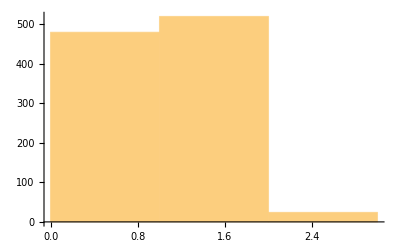

```mathematica
Histogram[Table[Block[{or=nthor[CompleteGraph[5],j]},VertexConnectivity[or]],{j,0,2^10-1}]]
```

```mathematica
3,3,
```

```mathematica
{0,1}
```

```mathematica
Sort[Map[First,Tally[Table[Block[{or=nthor[CompleteGraph[4],j]},Length[FindCycle[or,∞,All]]],{j,0,2^EdgeCount[CompleteGraph[4]]-1}]]]]
```

{0,1,3}

```mathematica
Sort[Map[First,Tally[Table[Block[{or=nthor[CompleteGraph[5],j]},Length[FindCycle[or,∞,All]]],{j,0,2^10-1}]]]]
```

{0,1,3,6,7,9,10,12}

```mathematica
Sort[Map[First,Tally[Table[Block[{or=nthor[CompleteGraph[6],j]},Length[FindCycle[or,∞,All]]],{j,0,2^EdgeCount[CompleteGraph[6]]-1}]]]]
```

{0,1,2,3,6,7,9,10,12,15,16,20,21,22,23,26,27,28,31,32,34}

```mathematica
Sort[Map[First,Tally[ParallelTable[Block[{or=nthor[CompleteGraph[7],j]},Length[FindCycle[or,∞,All]]],{j,0,2^EdgeCount[CompleteGraph[7]]-1}]]]]
```

{0,1,2,3,4,6,7,9,10,12,15,16,18,19,20,21,22,23,24,26,27,28,30,31,32,34,35,36,39,40,41,42,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,91,92,93,94,95,96,97,98,99,100,101,104,106,107,109,111,113,115,124,136}

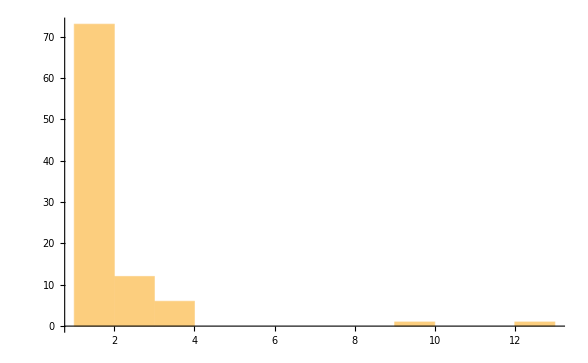

```mathematica
Histogram[Differences[{0,1,2,3,4,6,7,9,10,12,15,16,18,19,20,21,22,23,24,26,27,28,30,31,32,34,35,36,39,40,41,42,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,91,92,93,94,95,96,97,98,99,100,101,104,106,107,109,111,113,115,124,136}]]
```

```mathematica
2^EdgeCount[CompleteGraph[7]]
```

2097152

```mathematica
EdgeCount[CompleteGraph[4]]
```

6

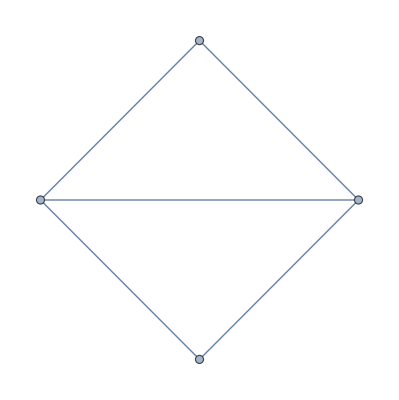

```mathematica
GraphData["DiamondGraph"]
```

Note the top orientation. Apparently, I wrote the program wrong because there's no path from 1->2 including (3,4).
However, it still seems that I have botched the lemma, as some trivial counterexamples still seem to apply...

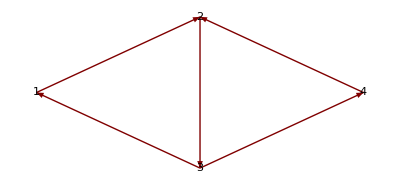
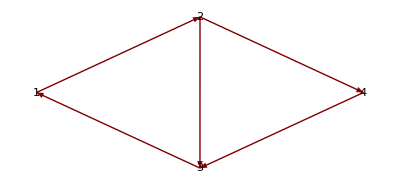
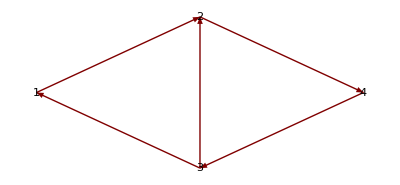
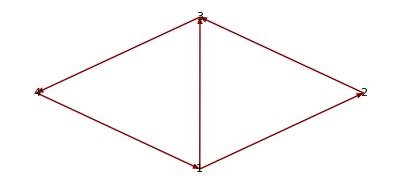
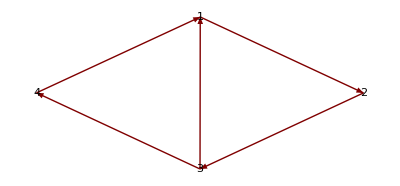
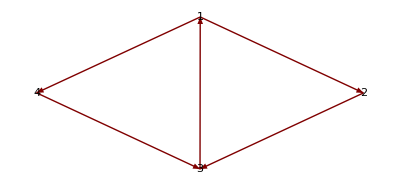
{-Graphics-,10,2,1,{{3->4,1,2,False},{3->4,2,1,False}}}
{-Graphics-,12,2,1,{{1->3,4,2,False},{4->1,2,3,False}}}
{-Graphics-,13,2,1,{{3->2,1,4,False},{2->4,3,1,False}}}
{-Graphics-,18,2,1,{{2->3,4,1,False},{4->2,1,3,False}}}
{-Graphics-,19,2,1,{{3->1,2,4,False},{1->4,3,2,False}}}
{-Graphics-,21,2,1,{{4->3,1,2,False},{4->3,2,1,False}}}

```mathematica
Select[Table[Block[{or=nthor[GraphData["DiamondGraph"],j]},{GraphPlot[or,VertexLabeling->True],j,Length[FindCycle[or,∞,All]],VertexConnectivity[or],checkL[or]}],{j,0,2^5-1}],Length[Last[#]]≠0&]//Column
```

```mathematica
Table[Length[FindCycle[nthor[CompleteGraph[4],i]]],{i,1,5}]
```

{0,1,0,0,1}

```mathematica
Tally[Table[Block[{or=nthor[CompleteGraph[4],j]},VertexConnectivity[or]],{j,0,2^EdgeCount[CompleteGraph[4]]-1}]]
```

{{0,40},{1,24}}

```mathematica
Tally[Table[Block[{or=nthor[CompleteGraph[5],j]},VertexConnectivity[or]],{j,0,2^EdgeCount[CompleteGraph[5]]-1}]]
```

{{0,480},{1,520},{2,24}}

```mathematica
Select[Table[Block[{or=nthor[CompleteGraph[5],j]},{j,VertexConnectivity[or]}],{j,0,2^EdgeCount[CompleteGraph[5]]-1}],Last[#]==2&]
```

{{200,2},{209,2},{226,2},{229,2},{332,2},{338,2},{341,2},{358,2},{394,2},{397,2},{403,2},{423,2},{600,2},{620,2},{626,2},{629,2},{665,2},{682,2},{685,2},{691,2},{794,2},{797,2},{814,2},{823,2}}

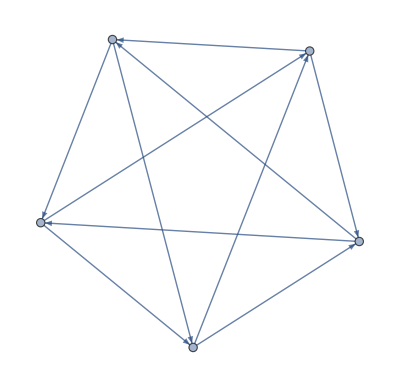

```mathematica
nthor[CompleteGraph[5],200]
```

```mathematica
Tally[Table[Block[{or=nthor[CompleteGraph[6],j]},VertexConnectivity[or]],{j,0,2^EdgeCount[CompleteGraph[6]]-1}]]
```

{{0,10448},{1,19332},{2,2988}}

```mathematica
Tally[ParallelTable[Block[{or=nthor[CompleteGraph[7],j]},VertexConnectivity[or]],{j,0,2^EdgeCount[CompleteGraph[7]]-1}]]
```

{{0,419664},{1,1240188},{2,434660},{3,2640}}

```mathematica
Reduce[{x3==x1+x2,
x4==x5+x6,
x7==x8+x9,
x10==x11+x12,
x13==x14+x15,
x16==x17+x18,
x1≥x9,
x5≥x15,
x8≥x2,
x11≥x18,
x14≥x6,
x17≥x12,
x3>x4,
x7>x10,
x13>x16,
x2>0,
x8>0,
x15>0,
x5>0,
x12>0,
x17>0,
x1≥0,
x6≥0,
x9≥0,
x11≥0,
x14≥0,
x18≥0},Integers]
```

```mathematica
cases3=%;
```

```mathematica
Map[Simplify[#,{(C[1]|C[2]|C[3]|C[4]|C[5]|C[6]|C[7]|C[8]|C[9]|C[10]|C[11]|C[12]|C[13]|C[14]|C[15]|C[16]|C[17]|C[18]|C[19]|C[20]|C[21]|C[22]|C[23]|C[24]|C[25]|C[26]|C[27]|C[28]|C[29]|C[30]|C[31]|C[32]|C[33]|C[34]|C[35]|C[36]|C[37]|C[38]|C[39]|C[40]|C[41]|C[42]|C[43]|C[44]|C[45]|C[46]|C[47]|C[48]|C[49]|C[50]|C[51]|C[52]|C[53]|C[54]|C[55]|C[56])∈Integers&&C[1]≥0&&C[2]≥0&&C[3]≥0&&C[4]≥0&&C[5]≥0&&C[6]≥0&&C[7]≥0&&C[8]≥0&&C[9]≥0&&C[10]≥0&&C[11]≥0&&C[12]≥0&&C[13]≥0&&C[14]≥0&&C[15]≥0&&C[16]≥0&&C[17]≥0&&C[18]≥0&&C[19]≥0&&C[20]≥0&&C[21]≥0&&C[22]≥0&&C[23]≥0&&C[24]≥0&&C[25]≥0&&C[26]≥0&&C[27]≥0&&C[28]≥0&&C[29]≥0&&C[30]≥0&&C[31]≥0&&C[32]≥0&&C[33]≥0&&C[34]≥0&&C[35]≥0&&C[36]≥0&&C[37]≥0&&C[38]≥0&&C[39]≥0&&C[40]≥0&&C[41]≥0&&C[42]≥0&&C[43]≥0&&C[44]≥0&&C[45]≥0&&C[46]≥0&&C[47]≥0&&C[48]≥0&&C[49]≥0&&C[50]≥0&&C[51]≥0&&C[52]≥0&&C[53]≥0&&C[54]≥0&&C[55]≥0&&C[56]≥0}]&,ToExpression[StringJoin["{",StringReplace[ToString[cases3],{"||"->","}],"}"]]]
```

```mathematica
First[%]
```

```mathematica
ToString[a&&x5==2+C[1]+C[2]+C[3]+C[4]+C[5]+C[6]+C[7]+C[8]+C[9]+C[10]+C[11]+C[12]+C[13]+C[14]+C[15]+C[32]+C[35]+C[36]+C[37]+C[38]+C[44]]
```

a && x5 == 2 + C[1] + C[2] + C[3] + C[4] + C[5] + C[6] + C[7] + C[8] + C[9] + C[10] + C[11] + C[12] + C[13] + C[14] + C[15] + C[32] + C[35] + C[36] + C[37] + C[38] + C[44]

```mathematica
#^2&@2
```

4

```mathematica
Map[{First[#],Last[#]}&@Map[Normal,CoefficientArrays[ToExpression[#]]]&,Map[StringJoin["{",#,"}"]&,Map[StringReplace[StringReplace[ToString[#],Map[#->","&,Table[StringJoin[" && x",ToString[i]," == "],{i,1,20}]]],Map[#->""&,Table[StringJoin["x",ToString[i]," == "],{i,1,20}]]]&,Out[251]]]]
```

```mathematica
Sort[Map[Last,Map[Tally,Map[First,Out[285]]]]]//Column
```

{2,3}
{2,4}
{2,5}
{3,1}
{3,1}
{3,1}
{3,1}
{3,1}
{3,1}
{3,2}
{3,2}
{3,2}
{3,2}
{3,2}
{3,2}
{3,2}
{3,2}
{3,4}
{3,4}
{3,4}
{3,4}

```mathematica
Last[First[Out[285]]]
```

```mathematica
ArrayPlot[First[DeleteDuplicates[Map[Last, Out[285]]]]]
```

-Graphics-

```mathematica
Length[DeleteDuplicates[Map[Last, Out[285]]]]
```

1

```mathematica
Last[%]
```

{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,1,0,0,0,0,0,0,1,0,0,1,0,0,0,0,0,1,0,0,0,0,1,0,0,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,1,1,0,1,1,0,0,0,1,0,1,1,0,1,1,0,0,0,0,1,0,0,0,0,1,0,0,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,1,0,1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,0,0,0,0,0,0,0,0,0},{1,1,0,1,1,0,1,1,1,0,1,1,0,1,1,0,1,1,1,0,1,0,1,0,0,1,0,1,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,1,1,1,1,0,1,0,0,0,0,0,0,0,1,1,0,0,1,0,0,0,0,1,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,1,0,1,1,1,1,1,1,1,0,1,0,0,0,0,0,0,1,1,1,1,0,1,1,1,1,0,0,0,0,1,1,0,0,1,1,1,1,0,1,1,1,1,0,0,0,0,0},{1,1,1,0,0,0,0,0,1,0,1,1,1,0,0,0,0,0,1,0,1,1,0,0,0,1,1,0,0,0,0,0,0,0,0,1,0,0,1,0,0,0,1,1,1,1,1,1,0,1,0,1,0,0,0,0},{1,1,1,1,0,0,1,0,1,0,1,1,1,1,0,0,1,0,1,0,1,1,1,0,0,1,1,1,0,0,1,1,1,1,1,1,0,0,1,0,0,0,1,1,1,1,1,1,0,1,0,1,0,0,0,0},{1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,0,0,0,0,0,0,0,0,0,0,1,1,1,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,1,0,0,0},{1,1,1,1,1,1,1,0,1,0,1,1,1,1,1,1,1,0,1,0,1,1,1,1,0,1,1,1,1,0,1,1,1,1,1,1,1,0,1,1,0,0,1,1,1,1,1,1,1,1,1,1,1,0,0,0},{1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,0,0,0,0,0,0,1,0,0,1,1,1,1,0,0,0,0,0,1,0,0,1,0,0,0,0,1,1,1,0,0},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,1,1,1,1,1,1,1,1,1,0,1,1,0,0,1,1,1,1,1,1,0,0,1,1,0,0,1,1,1,0,0,1,1,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,0,1,1,1,1,1,1,1,0,1,1,1,0,1,1,1,0,0,1,1,1,1,0},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,1,1,1,1,1,0,1,1,1,0,1,1,1,0,0,1,1,1,1,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,1,0,1,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,0,0,1,0,1,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,1,1,1,1,1}}

```mathematica
ArrayPlot[Out[268]]
```

-Graphics-

```mathematica
Reduce[{x3==x1+x2,
x4==x5+x6,
x7==x8+x9,
x10==x11+x12,
x13==x14+x15,
x16==x17+x18,
x1≥x9,
x5≥x15,
x8≥x2,
x11≥x18,
x14≥x6,
x17≥x12,
x3>x4,
x7>x10,
x13>x16,
x2>0,
x8>0,
x15>0,
x5>0,
x12>0,
x17>0,
x1≥0,
x6≥0,
x9≥0,
x11≥0,
x14≥0,
x18≥0}]
```

$Aborted

```mathematica
Length[FindCycle[Graph[{1->2,1->4,2->5,2->3,3->1,3->4,4->2,4->5,5->1,5->3}],∞,All]]
```

12

```mathematica
Max[Table[Length[FindCycle[nthor[CompleteGraph[5],i],∞,All]],{i,0,2^EdgeCount[CompleteGraph[5]]}]]
```

12

```mathematica
Reduce[n(n-1)/2<2n+3,Integers]
```

n==0||n==1||n==2||n==3||n==4||n==5

```mathematica
a+b+c
```

```mathematica
Reduce[{3≤e,e≤(3n-n^2-1)/(2-n),n≥3},Integers]
```

(e|n)∈Integers&&e≥3&&n≥(3+e)/2+1/2 √(5-2 e+e^2)

```mathematica
Reduce[{3≤e,e≤(3n-n^2-1)/(2-n),n≥3,e≤(n(n-1))/2},Integers]
```

(e|n)∈Integers&&e≥3&&n≥(3+e)/2+1/2 √(5-2 e+e^2)

```mathematica
Reduce[{3≤e,e≤(3n-n^2-1)/(2-n),n≥3,e≤(n(n-1))/2},e,Integers]
```

(n|e)∈Integers&&n≥5&&3≤e≤(1-3 n+n^2)/(-2+n)

```mathematica
Table[{e,Ceiling[(3+e)/2+1/2 √(5-2 e+e^2)]},{e,3,20}]
```

{{3,5},{4,6},{5,7},{6,8},{7,9},{8,10},{9,11},{10,12},{11,13},{12,14},{13,15},{14,16},{15,17},{16,18},{17,19},{18,20},{19,21},{20,22}}

```mathematica
Reduce[{n≥e+2,n>2,e>2},e,Integers]
```

(C[1]|C[2])∈Integers&&C[1]≥0&&C[2]≥0&&n==5+C[1]+C[2]&&e==3+C[2]

```mathematica
n≥e+2≥3
3≤e+2≤n
e+2≤n
e≤n-2
```

```mathematica
Reduce[{3≤e,e≥n,e≤(3n-n^2-1)/(2-n),n≥3,e≤(n(n-1))/2},Integers]
```

False

```mathematica
Reduce[{
3≤n,
3≤e,
e≥n,
c==e-n,
(*(3+2c)/n≤ps,*)
c≤ps,
ps+2≤e2,
e2==c+1},n,Integers]
```

False

```mathematica
Table[{e,Floor[1/2 (-1+e)-1/2 √(-11-6 e+e^2)]},{e,8,20}]
```

{{8,2},{9,2},{10,1},{11,1},{12,1},{13,1},{14,1},{15,1},{16,1},{17,1},{18,1},{19,1},{20,1}}

```mathematica
Reduce[((c|e|e2|ps|n)∈Integers&&e2==1+c&&n==-c+e&&e≥8&&1<c&&c≤e/3&&-3-2 c≤ps c-ps e&&ps≤-1+c)]
```

(c|e|ps)∈Integers&&((c==2&&((e==8&&ps≤1)||(e==9&&ps≤1)||(e≥10&&ps≤-7/(2-e))))||(c≥3&&e≥3 c&&ps≤(-3-2 c)/(c-e)))&&e2==1+c&&n==-c+e

```mathematica
Reduce[1/2 (-1+e)-1/2 √(-11-6 e+e^2)==c,e,Integers]
```

(c|e)∈Integers&&((c≤-2&&e==(3+c+c^2)/(-1+c))||(c==2&&e==9))

```mathematica
e==n(n-1)/2
```

```mathematica
Reduce[{
e≤n(n-1)/2,
n>5,(*assuming I've checked these cases already*)
e≥n,
ps≥1,
e≥n(n-1)/2-(n-1-2),
e==c+n,
ps≥(c (2 c-n+n^2))/(2 n^2),
ps≤n},Integers]
```

(c==6&&e==12&&n==6&&ps==4)||(c==6&&e==12&&n==6&&ps==5)||(c==6&&e==12&&n==6&&ps==6)||(c==7&&e==13&&n==6&&ps==5)||(c==7&&e==13&&n==6&&ps==6)||(c==8&&e==14&&n==6&&ps==6)||(c==9&&e==15&&n==6&&ps==6)||(c==10&&e==17&&n==7&&ps==7)

```mathematica
(*If we can only get (n-1) as max number of paths*)
Reduce[{
e≤n(n-1)/2,
n≥3,
e≥n,
ps≥1,
e≥n(n-1)/2-(n-1-2),
e==c+n,
ps≥(c (2 c-n+n^2))/(2 n^2),
ps≤n-1},Integers]
```

(c==0&&e==3&&n==3&&ps==1)||(c==0&&e==3&&n==3&&ps==2)||(c==1&&e==5&&n==4&&ps==1)||(c==1&&e==5&&n==4&&ps==2)||(c==1&&e==5&&n==4&&ps==3)||(c==2&&e==6&&n==4&&ps==1)||(c==2&&e==6&&n==4&&ps==2)||(c==2&&e==6&&n==4&&ps==3)||(c==3&&e==8&&n==5&&ps==2)||(c==3&&e==8&&n==5&&ps==3)||(c==3&&e==8&&n==5&&ps==4)||(c==4&&e==9&&n==5&&ps==3)||(c==4&&e==9&&n==5&&ps==4)||(c==5&&e==10&&n==5&&ps==3)||(c==5&&e==10&&n==5&&ps==4)||(c==6&&e==12&&n==6&&ps==4)||(c==6&&e==12&&n==6&&ps==5)||(c==7&&e==13&&n==6&&ps==5)

```mathematica
Reduce[{
e≤n(n-1)/2,
n≥3,
e≥n,
ps≥1,
e≥n(n-1)/2-(n-1-2),
e==c+n,
ps≥(c (2 c-n+n^2))/(2 n^2),
ps≤n-2},Integers]
```

(c==0&&e==3&&n==3&&ps==1)||(c==1&&e==5&&n==4&&ps==1)||(c==1&&e==5&&n==4&&ps==2)||(c==2&&e==6&&n==4&&ps==1)||(c==2&&e==6&&n==4&&ps==2)||(c==3&&e==8&&n==5&&ps==2)||(c==3&&e==8&&n==5&&ps==3)||(c==4&&e==9&&n==5&&ps==3)||(c==5&&e==10&&n==5&&ps==3)||(c==6&&e==12&&n==6&&ps==4)

```mathematica
Reduce[{
e≤n(n-1)/2,
n≥3,
e≥n,
ps≥1,
e==c+n,
ps≥(c (2 c-n+n^2))/(2 n^2),
ps≤n-2},Integers]
```

(c|e|n|ps)∈Integers&&((n==3&&e==3&&ps==1&&c==0)||(n==4&&((e==4&&((ps==1&&c==0)||(ps==2&&c==0)))||(e==5&&((ps==1&&c==1)||(ps==2&&c==1)))||(e==6&&((ps==1&&c==2)||(ps==2&&c==2)))))||(n==5&&((e==5&&((ps==1&&c==0)||(ps==2&&c==0)||(ps==3&&c==0)))||(e==6&&((ps==1&&c==1)||(ps==2&&c==1)||(ps==3&&c==1)))||(e==7&&((ps==1&&c==2)||(ps==2&&c==2)||(ps==3&&c==2)))||(e==8&&((ps==2&&c==3)||(ps==3&&c==3)))||(e==9&&ps==3&&c==4)||(e==10&&ps==3&&c==5)))||(n≥6&&((n≤e≤1/4 (5 n-n^2)+1/4 √(17 n^2-2 n^3+n^4)&&1≤ps≤-2+n&&c==e-n)||(1/4 (5 n-n^2)+1/4 √(17 n^2-2 n^3+n^4)<e<1/4 (5 n-n^2)+1/4 √(-31 n^2+14 n^3+n^4)&&(2 e^2-5 e n+3 n^2+e n^2-n^3)/(2 n^2)≤ps≤-2+n&&c==e-n)||(e==1/4 (5 n-n^2)+1/4 √(-31 n^2+14 n^3+n^4)&&ps==-2+n&&c==-n+1/4 (5 n-n^2)+1/4 √(-31 n^2+14 n^3+n^4)))))

```mathematica
Expand[(c (2 c-n+n^2))/(2 n^2)]
```

c/2+c^2/n^2-c/(2 n)

```mathematica
Reduce[{
e≤n(n-1)/2,
n≥3,
e≥n,
ps≥1,
e==c+n,
ps≥(c (2 c-n+n^2))/(2 n^2),
ps≤49c/100},Integers]
```

False

```mathematica
Reduce[{
e≤n(n-1)/2,
n≥3,
e≥n,
ps≥1,
e==c+n,
ps≥(c (2 c-n+n^2))/(2 n^2),
ps≤c-10},Integers]
```

```mathematica
Reduce[{
e≤n(n-1)/2,
n≥3,
e≥n,
ps≥1,
e==c-n,
ps≥(c (2 c-n+n^2))/(2 n^2),
ps≤c},Integers]
```

(c|e|n|ps)∈Integers&&n≥3&&((n≤e<1/2 (-n+n^2)&&(2 e^2+3 e n+n^2+e n^2+n^3)/(2 n^2)≤ps≤e+n&&c==e+n)||(e==1/2 (-n+n^2)&&ps==(n^2+n^3+3/2 n (-n+n^2)+1/2 n^2 (-n+n^2)+1/2 (-n+n^2)^2)/(2 n^2)&&c==n+1/2 (-n+n^2)))

```mathematica
FindInstance[{3≤n≤e,(2 e^2+3 e n+n^2+e n^2+n^3)/(2 n^2)≤e+n},{e,n},Integers]
```

{{e→4,n→4}}

```mathematica
2 e^2+3 e n+n^2+e n^2≤2 n^2 e+n^3
2 e^2+3 e n+n^2≤2 n^2 e+n^3
2 e^2≤2 n^2 e+n^3-3 e n-n^2
2 e^2≤n(2n e+n^2-3 e-n)
0≤n(2n e+n^2-3 e-n)-2 e^2
```

```mathematica
Factor[n(2n e+n^2-3 e-n)-2 e^2]
```

-(2 e+n) (e+n-n^2)

```mathematica
n(n-1)>e
```

```mathematica
Table[(n^2+n^3+3/2 n (-n+n^2)+1/2 n^2 (-n+n^2)+1/2 (-n+n^2)^2)/(2 n^2),{n,3,10}]
```

{6,10,15,21,28,36,45,55}

```mathematica
Reduce[{3≤n,
3≤e,
e≥n,
2e≤n(n-1),
e≥(n-n^2-1)/(2-n)},Integers]
```

(e|n)∈Integers&&n≥5&&(1-n+n^2)/(-2+n)≤e≤1/2 (-n+n^2)

```mathematica
Reduce[{3≤n,3≤e,e≥n,c==e-n,e≤(n(n-1))/2,ps≥(1+2c)/n,ps≥c+1},Integers]
```

(c|e|ps)∈Integers&&c≥0&&e≥1/2 (3+2 c)+1/2 √(9+8 c)&&n==-c+e&&ps≥1+c

```mathematica
Reduce[{3≤n,3≤e,e≥n,c+1≥(1+2c)/n,ps+2≥e,c==e-n,e≤(n(n-1))/2},Integers]
```

((e|ps)∈Integers&&c==0&&e≥3&&n==e&&ps≥-2+e)||((c|e|ps)∈Integers&&c≥1&&e≥1/2 (3+2 c)+1/2 √(9+8 c)&&n==-c+e&&ps≥-2+e)

```mathematica
Reduce[{3≤n,3≤e,e≥n,ps≥(1+2c)/n,ps+2≥e,c==e-n,e-2==c+1,e≤(n(n-1))/2},Integers]
```

C[1]∈Integers&&C[1]≥1&&c==0&&ps==C[1]&&e==3&&n==3

```mathematica
Reduce[{3≤n,3≤e,e≥n,ps≥(1+2c)/n,ps+1≥e,c==e-n,e-2==c+1,e≤(n(n-1))/2},Integers]
```

C[1]∈Integers&&C[1]≥2&&c==0&&ps==C[1]&&e==3&&n==3

```mathematica
Reduce[{3≤n,3≤e,e≥n,ps≥(1+2c)/n,ps+0≥e,c==e-n,e-2==c+1,e≤(n(n-1))/2},Integers]
```

C[1]∈Integers&&C[1]≥3&&c==0&&ps==C[1]&&e==3&&n==3

```mathematica
∑_(j=2)^(i-1) (n-j)≤c≤∑_(j=2)^i (n-j)
```

1/2 (2+i-i^2-4 n+2 i n)≤c≤1/2 (2-i-i^2-2 n+2 i n)

```mathematica
2+i-i^2-4 n+2 i n≤2c≤2-i-i^2-2 n+2 i n
2+i-i^2-4 n+2 i n≤2c≤2-i-i^2-2 n+2 i n
```

```mathematica
Reduce[{2+i-i^2-4 n+2 i n≤2c≤2-i-i^2-2 n+2 i n,2≤i≤n-1,n≥5,c≥1,c≤n(n-3)/2},{i},Integers]
```

(c|n|i)∈Integers&&n≥5&&((1≤c≤-2+n&&2≤i≤1/2 (1+2 n)-1/2 √(9-8 c-12 n+4 n^2))||(-2+n<c≤1/2 (-3 n+n^2)&&1/2 (-1+2 n)-1/2 √(9-8 c-12 n+4 n^2)≤i≤1/2 (1+2 n)-1/2 √(9-8 c-12 n+4 n^2)))

```mathematica
LogicalExpand[%]
```

((c|n|i)∈Integers&&n≥5&&-2+n<c&&c≤1/2 (-3 n+n^2)&&i≤1/2 (1+2 n)-1/2 √(9-8 c-12 n+4 n^2)&&1/2 (-1+2 n)-1/2 √(9-8 c-12 n+4 n^2)≤i)||((c|n|i)∈Integers&&n≥5&&1≤c&&2≤i&&c≤-2+n&&i≤1/2 (1+2 n)-1/2 √(9-8 c-12 n+4 n^2))

```mathematica
Reduce[{2+i-i^2-4 n+2 i n≤2c≤2-i-i^2-2 n+2 i n,2≤i≤n-1,n≥5,c≥1,c≤n(n-3)/2,ps==c i+∑_(j=2)^i j(n-j),c≥(-3+n) (-2+n)/2},{ps},Integers]
(*ps==c i+∑_(j=2)^i j(n-j)*)
```

```mathematica
LogicalExpand[%]
```

```mathematica
FullSimplify[c≥n(n-1)/2-(n-1-2)-n]
```

2 c≥(-3+n) (-2+n)

# GO HERE.

```mathematica
"Additional condition of e≥n(n-1)/2-(n-1-2), because we need at least this many edges because we're guaranteed that a C_{n-1} needs to be filled out into a clique, or else the induction wouldn't follow to the next spot and because it's induction, we've assumed that it has.";
"Use Menger's theorem (http://math.fau.edu/locke/Menger.htm): 'Directed, Vertex Version. Let D be a directed graph, and let u and v be vertices in G, with no arc from u to v. Then, the maximum number of pairwise-internally-disjoint directed (u,v)-paths in D equals the minimum number of vertices from V(D)-{u,v} whose deletion destroys all directed paths from u to v.'

Wanting #Ps[v0,v0'], we consider D := D_0 - e_0, which has #Ps[e_0]-1 paths from v0 to v0'.
Because deleting all the vertices other than v0 and v0' will remove all paths between them (for a total of n-2 vertices), there are at most n-1 paths from v0 to v0'.";
```

```mathematica
"
  '2+i-i^2-4 n+2 i n≤2c≤2-i-i^2-2 n+2 i n'  by the condition for the (ps) pigeon hole inequality.
'2≤i≤n-1'                               also by the condition of the above inequality.
  'n≥5'                                   to get rid of the small, already proven cases.
  'c≥1'                                   because with no chords, it easily holds.
  'c≤n(n-3)/2'                            because chords plus cycle edges can't be more than n(n-1)/2 because digraph is simple.
  'ps*n≥c i+∑_(j = 2)^i j(n-j)'                    by the pigeon hole chord (ps) inequality.
  'c≥(-3+n) (-2+n)/2'                    because a clique of chords wasn't even enough for a single edge to satisfy the counterexample requirements.
  'ps≤n-1'                               by menger's theorem.
"
```

```mathematica
Reduce[{2+i-i^2-4 n+2 i n≤2c≤2-i-i^2-2 n+2 i n,2≤i≤n-1,n≥5,c≥1,c≤n(n-3)/2,ps*n≥c i+∑_(j=2)^i j(n-j),c≥(-3+n) (-2+n)/2,ps≤n-1},Integers]
```

(c==3&&i==2&&n==5&&ps==3)||(c==3&&i==2&&n==5&&ps==4)

```mathematica
Reduce[{2+i-i^2-4 n+2 i n≤2c≤2-i-i^2-2 n+2 i n,2≤i≤n-1,n≥5,c≥1,c≤n(n-3)/2,ps≥c i+∑_(j=2)^i j(n-j),c≥(-3+n) (-2+n)/2,ps≤n-1},Integers]
```

False

```mathematica
LogicalExpand[%]
```

False

```mathematica
Reduce[{2+i-i^2-4 n+2 i n≤2c≤2-i-i^2-2 n+2 i n,2≤i≤n-1,n≥3,c≥1,c≤n(n-3)/2,ps≥c i+∑_(j=2)^i j(n-j),c≥(-3+n) (-2+n)/2,ps≤n-1},Integers]
```

False

```mathematica
"HERE";
```

```mathematica
"There are 'n' of each option and the theorem still holds.";
```

```mathematica
Reduce[{i n-n≤2c≤i n,2≤i≤n-1,n≥3,c≥1,c≤n(n-3)/2,ps≥(c-(i-1)) i+∑_(j=2)^(i-1) (n-j),c≥(-3+n) (-2+n)/2,ps≤n-1},Integers]
```

(c==2&&i==2&&n==4&&ps==2)||(c==2&&i==2&&n==4&&ps==3)||(c==3&&i==2&&n==5&&ps==4)

```mathematica
"Without the lower bound on number of chords";
Reduce[{i n-n≤2c≤i n,2≤i≤n-1,n≥3,c≥1,c≤n(n-3)/2,ps≥(c-(i-1)) i+∑_(j=2)^(i-1) (n-j),(*c≥(-3+n) (-2+n)/2,*)ps≤n-1},Integers]
```

(c==2&&i==2&&n==4&&ps==2)||(c==2&&i==2&&n==4&&ps==3)||((c|n|ps)∈Integers&&c≥3&&i==2&&n==-1+2 c&&ps==2 (-1+c))||((c|n|ps)∈Integers&&c≥3&&i==2&&n==2 c&&ps==2 (-1+c))||((c|n|ps)∈Integers&&c≥3&&i==2&&n==2 c&&ps==-1+2 c)

```mathematica
LogicalExpand[%]
```

(c==2&&i==2&&n==4&&ps==2)||(c==2&&i==2&&n==4&&ps==3)||((c|n|ps)∈Integers&&i==2&&n==2 c&&ps==2 (-1+c)&&c≥3)||((c|n|ps)∈Integers&&i==2&&n==2 c&&ps==-1+2 c&&c≥3)||((c|n|ps)∈Integers&&i==2&&n==-1+2 c&&ps==2 (-1+c)&&c≥3)

```mathematica
"
i n-n≤2c≤i n           pigeonhole inequality for i 
2≤i≤n-1                limits of i
n≥3                    smallest cycle is a triangle
c≥1                    have at least one chord because only cycle doesn't work
c≤n(n-3)/2             don't have more chords than in a clique
n-2≥f≥2                the first chord behaves like i in limits
c≥f(f-3)/2             the first chord guarantees a clique, by induction
ps≥1/n∑_(k = f)^(n - 2) (f+k)           the first chord inducted gives a cascade of chords
c≥n-2-f                there must be at least as many chords as in the cascade of chords
ps≥(c-(i-1)) i+∑_(j = 2)^(i - 1) (n-j) pigeonhole inequality
ps≤n-1                 menger's theorem
";
```

```mathematica
"c≥(f+1)(f-2)/2 because a chord size f gives a cycle size (f+1)?";
```

```mathematica
Reduce[{i n-n≤2c≤i n,2≤i≤n-1,n≥3,c≥1,c≤n(n-3)/2,n-2≥f≥2,c≥(f+1)(f-2)/2,ps≥1/n∑_(k=f)^(n-2) (f+k),c≥n-2-f,ps≥(c-(i-1)) i+∑_(j=2)^(i-1) (n-j),(*c≥(-3+n) (-2+n)/2,*)ps≤n-1},Integers]
```

```mathematica
Reduce[{i n-n≤2c≤i n,2≤i≤n-1,n≥3,c≥1,c≤n(n-3)/2,n-2≥f≥2,c≥f(f-3)/2,ps≥1/n∑_(k=f)^(n-2) (f+k),c≥n-2-f,ps≥(c-(i-1)) i+∑_(j=2)^(i-1) (n-j),(*c≥(-3+n) (-2+n)/2,*)ps≤n-1},Integers]
```

```mathematica
Reduce[{i n-n≤2c≤i n,2≤i≤n-1,n≥3,c≥1,c≤n(n-3)/2,n-2≥f≥2,c≥f(f-3)/2,ps≥1/n∑_(k=f)^(n-2) (f+k),c≥n-2-f+(5),ps≥(c-(i-1)) i+∑_(j=2)^(i-1) (n-j),(*c≥(-3+n) (-2+n)/2,*)ps≤n-1},Integers]
```

False

```mathematica
"Below is the case where there's no guaranteed triangle (if the conjecture of c≥1/2 (-3+n) (-2+n) guarantees a triangle is true, that is).";
```

```mathematica
Reduce[{i n-n≤2c≤i n,2≤i≤n-1,n≥5,c≥1,c≤n(n-3)/2,ps≥(c-(i-1)) i+∑_(j=2)^(i-1) (n-j),c<1/2 (-3+n) (-2+n),ps≤n-1},Integers]
```

(c==3&&i==2&&n==6&&ps==4)||(c==3&&i==2&&n==6&&ps==5)||(c==4&&i==2&&n==7&&ps==6)||(c==4&&i==2&&n==8&&ps==6)||(c==4&&i==2&&n==8&&ps==7)||(c==5&&i==2&&n==9&&ps==8)||(c==5&&i==2&&n==10&&ps==8)||(c==5&&i==2&&n==10&&ps==9)||(c==6&&i==2&&n==11&&ps==10)||(c==6&&i==2&&n==12&&ps==10)||(c==6&&i==2&&n==12&&ps==11)||((c|n|ps)∈Integers&&c≥7&&i==2&&n==-1+2 c&&ps==2 (-1+c))||((c|n|ps)∈Integers&&c≥7&&i==2&&n==2 c&&ps==2 (-1+c))||((c|n|ps)∈Integers&&c≥7&&i==2&&n==2 c&&ps==-1+2 c)

```mathematica
"
f==n-2                           induction hypothesis guarantees subcycle of this size
1≤cf+1≤c                        relation of subcycle chords to total chords
2≤k≤n-4                         piegeonhole lemma bounds for subcycle
(k-1)(n-1)≤cf≤k(n-2)            piegeonhole lemma bounds for subcycle
n-3≥psf≥(n-2-(k-1)) k+∑_(j = 2)^(k - 1) (n-1-j) pigeonhole lemma applied to the subcycle
";
```

```mathematica
Reduce[{i n-n≤2c≤i n,2≤i≤n-1,n≥5,c≥1,c≤n(n-3)/2,ps≥(c-(i-1)) i+∑_(j=2)^(i-1) (n-j),(*c≥(-3+n) (-2+n)/2,*)ps≤n-1,f==n-2,1≤cf+1≤c,2≤k≤n-4,(k-1)(n-1)≤cf≤k(n-2),n-3≥psf≥(n-2-(k-1)) k+∑_(j=2)^(k-1) (n-1-j)},Integers]
```

False

```mathematica
"This is by the handshake lemma (∑_(i = 1)^n (SuperscriptBox[d, +])_i == |E|) and because (d^+)_i≥2 so |E| ≥ 2n.
";
```

```mathematica
Reduce[{i n-n≤2c≤i n,2≤i≤n-1,n≥3,c≥1,c≤n(n-3)/2,ps≥(c-(i-1)) i+∑_(j=2)^(i-1) (n-j),(*c≥(-3+n) (-2+n)/2,*)ps≤n-1,2n≤e,e-n==c},Integers]
```

False

```mathematica
i n-n<=2c<=i n,2<=i<=n-1,n>=3,c>=1,c<=n (n-3)/2,ps>=(c-(i-1)) i+∑_(j=2)^(i-1) (n-j),(*c≥(-3+n) (-2+n)/2,*)ps<=n-1,2n<=e,e-n==c
```

```mathematica
i n - n <= 2 c <= i n, 2 <= i <= n - 1, n >= 3, c >= 1, c <= 
 n (n - 3)/2, ps >= (c - (i - 1)) i + ∑_(j=2)^(i-1) (n-j),(*c≥(-3+n) (-2+n)/2,*)ps <= n - 1, 2 n <= e,
 e - n == c
```

```mathematica
Reduce[{i n-n≤2c≤i n,2≤i≤n-1,n≥5,c≥1,c≤n(n-3)/2,ps≥(c-(i-1)) i+∑_(j=2)^(i-1) (n-j),(*c≥(-3+n) (-2+n)/2,*)ps≤n-1,2n≤e,e-n==c},Integers]
```

False

```mathematica
$$n>3$$
$$c\geq 1$$
$$c\leq n (n-3)/2$$
$$ps\geq\frac{2 k (k+c)-n (k^2+k+2)}{2n}$$
$$2\leq k\leq n-2$$
$$k (n-1)\leq c\leq k n$$
$$ps+1\leq n-1$$
$$n\leq c$$
```

```mathematica
Reduce[{n>9,
n≤c≤ n (n-3)/2,
ps≥(2 k (k+c)-n (k^2+k+2))/(2n),
2≤ k≤ n-2,
k (n-1)≤2 c≤ k n,
1≤ps+1≤ n-1},Integers]
```

(c|k|n|ps)∈Integers&&n≥10&&((k==2&&c==n&&0≤ps≤-2+n)||(2<k<(2 n)/(-1+n)&&n≤c≤(k n)/2&&0≤ps≤-2+n)||(k==(2 n)/(-1+n)&&((c==1/2 (-(2 n)/(-1+n)+(2 n^2)/(-1+n))&&0≤ps≤-2+n)||(n<c≤n^2/(-1+n)&&0≤ps≤-2+n)))||((2 n)/(-1+n)<k≤n/4+1/4 √(16 n+n^2)&&1/2 (-k+k n)≤c≤(k n)/2&&0≤ps≤-2+n)||(n/4+1/4 √(16 n+n^2)<k≤-3+n&&((1/2 (-k+k n)≤c≤(-2 k^2+2 n+k n+k^2 n)/(2 k)&&0≤ps≤-2+n)||((-2 k^2+2 n+k n+k^2 n)/(2 k)<c≤(k n)/2&&(2 c k+2 k^2-2 n-k n-k^2 n)/(2 n)≤ps≤-2+n)))||(-3+n<k<(-4 n+n^2)/(2 (-2+n))+1/2 √((16 n+8 n^2-8 n^3+n^4)/(-2+n)^2)&&((1/2 (-k+k n)≤c≤(-2 k^2+2 n+k n+k^2 n)/(2 k)&&0≤ps≤-2+n)||((-2 k^2+2 n+k n+k^2 n)/(2 k)<c≤1/2 (-3 n+n^2)&&(2 c k+2 k^2-2 n-k n-k^2 n)/(2 n)≤ps≤-2+n)))||((-4 n+n^2)/(2 (-2+n))+1/2 √((16 n+8 n^2-8 n^3+n^4)/(-2+n)^2)≤k<(-3 n+n^2)/(-1+n)&&1/2 (-k+k n)≤c≤1/2 (-3 n+n^2)&&0≤ps≤-2+n)||(k==(-3 n+n^2)/(-1+n)&&c==1/2 (-(-3 n+n^2)/(-1+n)+(n (-3 n+n^2))/(-1+n))&&0≤ps≤-2+n))

```mathematica
{n,2}
{n,3}
{n,4}
```

```mathematica
{0n≤c≤1n,2c}
{1n≤c≤2n,2n+(c-n)3}
{2n≤c≤3n,2n+3n+(c-2n)4}
{3n≤c≤4n,2n+3n+4n+(c-3n)5}
{4n≤c≤5n,2n+3n+4n+5n+(c-4n)6}
```

```mathematica
{k n≤c≤(k+1)n,(∑_(j=2)^(k+1) (j n))+(c-k n)(k n+2)}
```

```mathematica
{k n≤c≤(k+1)n,(∑_(j=2)^(k+1) (j n))+(c-k n)(k n+2)}
1≤k+1≤n-2
```

```mathematica
FullSimplify[(∑_(j=2)^(k+1) (j n))+(c-k n)(k n+2)]
```

1/2 k n (-1+k-2 k n)+c (2+k n)

```mathematica
1≤k+1≤n-2
k n≤c≤(k+1)n
1/2 k n (-1+k-2 k n)+c (2+k n)
```

```mathematica
Reduce[{n>3,c==n(n-3)/2,
1≤k+1≤n-2,
k n≤c≤(k+1)n,
ps*n≥1/2 k n (-1+k-2 k n)+c (2+k n)},Integers]
```

(C[2]∈Integers&&C[2]≥1&&c==2&&k==0&&n==4&&ps==C[2])||(C[2]∈Integers&&C[2]≥2&&c==5&&k==0&&n==5&&ps==C[2])||((C[1]|C[2])∈Integers&&C[1]≥1&&C[2]≥3 C[1]+2 C[1]^2&&c==1/2 (-3 (3+4 C[1])+(3+4 C[1])^2)&&k==2 C[1]&&n==3+4 C[1]&&ps==C[2])||((C[1]|4 (1+C[1])|C[2])∈Integers&&C[1]≥1&&C[2]≥1+7 C[1]+6 C[1]^2&&c==1/2 (-12 (1+C[1])+16 (1+C[1])^2)&&k==2 C[1]&&n==4 (1+C[1])&&ps==C[2])||((C[1]|C[2])∈Integers&&C[1]≥1&&C[2]≥2+13 C[1]+10 C[1]^2&&c==1/2 (-3 (5+4 C[1])+(5+4 C[1])^2)&&k==2 C[1]&&n==5+4 C[1]&&ps==C[2])||((C[1]|C[2])∈Integers&&C[1]≥0&&C[2]≥2+5 C[1]+2 C[1]^2&&c==1/2 (-3 (5+4 C[1])+(5+4 C[1])^2)&&k==1+2 C[1]&&n==5+4 C[1]&&ps==C[2])||((C[1]|2 (3+2 C[1])|C[2])∈Integers&&C[1]≥0&&C[2]≥6+13 C[1]+6 C[1]^2&&c==1/2 (-6 (3+2 C[1])+4 (3+2 C[1])^2)&&k==1+2 C[1]&&n==2 (3+2 C[1])&&ps==C[2])||((C[1]|C[2])∈Integers&&C[1]≥0&&C[2]≥11+23 C[1]+10 C[1]^2&&c==1/2 (-3 (7+4 C[1])+(7+4 C[1])^2)&&k==1+2 C[1]&&n==7+4 C[1]&&ps==C[2])

```mathematica
FindInstance[{n>8,
n≤c≤ n (n-3)/2,
2(**)≤k+1≤n-2,
k n≤c≤(k+1)n,
ps*n≥1/2 k n (-1+k-2 k n)+c (2+k n),
1≤ps+1≤ n-1},{n,c,k,ps},Integers,20]//TableForm
```

n→1894 | c→3882 | k→2 | ps→1892
n→217 | c→297 | k→1 | ps→179
n→1930 | c→1930 | k→1 | ps→1928
n→1376 | c→1376 | k→1 | ps→1374
n→1563 | c→1563 | k→1 | ps→1561
n→1453 | c→2995 | k→2 | ps→1451
n→849 | c→878 | k→1 | ps→113
n→1011 | c→1022 | k→1 | ps→1009
n→1165 | c→2345 | k→2 | ps→1163
n→1817 | c→1817 | k→1 | ps→53
n→142 | c→142 | k→1 | ps→2
n→1930 | c→1930 | k→1 | ps→19
n→1000 | c→2042 | k→2 | ps→95
n→699 | c→699 | k→1 | ps→17
n→1000 | c→2042 | k→2 | ps→998
n→977 | c→2012 | k→2 | ps→213
n→142 | c→142 | k→1 | ps→82
n→1563 | c→1563 | k→1 | ps→2
n→819 | c→914 | k→1 | ps→174
n→699 | c→699 | k→1 | ps→2

```mathematica
Reduce[{n≥5,
n≤c≤ n (n-3)/2,
1(**)≤k+1≤n-2,
k n≤c≤(k+1)n,
ps*n≥1/2 k n (-1+k-2 k n)+c (2+k n),
1≤ps+1≤ n-1,

n-2≥f≥2,
cf+1≤c,
(f+1)≤cf≤ (f+1) ((f+1)-3)/2,
1(**)≤fk+1≤(f+1)-2,
fk (f+1)≤cf≤(fk+1)(f+1),
psf*(f+1)≥1/2 fk (f+1) (-1+fk-2 fk (f+1))+cf (2+fk (f+1)),
1≤psf+1≤ (f+1)-1},Integers]
```

$Aborted

```mathematica
Resolve[Exists[{n,c,k,ps,f,cf,fk,psf},{n≥5,
n≤c≤ n (n-3)/2,
1(**)≤k+1≤n-2,
k n≤c≤(k+1)n,
ps*n≥1/2 k n (-1+k-2 k n)+c (2+k n),
1≤ps+1≤ n-1,

n-2≥f≥2,
cf+1≤c,
(f+1)≤cf≤ (f+1) ((f+1)-3)/2,
1(**)≤fk+1≤(f+1)-2,
fk (f+1)≤cf≤(fk+1)(f+1),
psf*(f+1)≥1/2 fk (f+1) (-1+fk-2 fk (f+1))+cf (2+fk (f+1)),
1≤psf+1≤ (f+1)-1}],Integers]
```

```mathematica
Resolve[Exists[{n,c,k,ps,f,cf,fk,psf},n≥5&&
n≤c≤ n (n-3)/2&&
1(**)≤k+1≤n-2&&
k n≤c≤(k+1)n&&
ps*n≥1/2 k n (-1+k-2 k n)+c (2+k n)&&
1≤ps+1≤ n-1&&
n-2≥f≥2&&
cf+1≤c&&
(f+1)≤cf≤ (f+1) ((f+1)-3)/2&&
1(**)≤fk+1≤(f+1)-2&&
fk (f+1)≤cf≤(fk+1)(f+1)&&
psf*(f+1)≥1/2 fk (f+1) (-1+fk-2 fk (f+1))+cf (2+fk (f+1))&&
1≤psf+1≤ (f+1)-1],Integers]
```

True

```mathematica
"
If for some n≥3, a cycle size n guarantees that, for any set of chords, either
	the existence of an edge that has too many paths through it to be in a clique of size n and still be a counterexample
Then, because the only thing that really changes is the allowance of more chords???, for a cycle of size (n+1) to be a counterexample, then it must have at least as many chords?

If n increases,

n≤c≤ n (n-3)/2&&                        more chords are allowed
1(**)≤k+1≤n-2&&                       
k n≤c≤(k+1)n&&                        
ps*n≥1/2 k n (-1+k-2 k n)+c (2+k n)&& more paths are required
1≤ps+1≤ n-1&&                        more paths are allowed

"
```

```mathematica
Reduce[{n≥10,
n≤c==(n-1) ((n-1)-3)/2,
1≤k+100==(n-1)-2,
0<ps==(1/2 k (n-1) (-1+k-2 k (n-1))+c (2+k (n-1)))/(n-1)},ps,Integers,Backsubstitution->True]
```

(c==5049&&k==0&&n==103&&ps==99)||(c==5150&&k==1&&n==104&&ps==5147)||(c==5252&&k==2&&n==105&&ps==10190)||(c==5355&&k==3&&n==106&&ps==15225)||(c==5459&&k==4&&n==107&&ps==20249)||(c==5564&&k==5&&n==108&&ps==25259)||(c==5670&&k==6&&n==109&&ps==30252)||(c==5777&&k==7&&n==110&&ps==35225)||(c==5885&&k==8&&n==111&&ps==40175)||(c==5994&&k==9&&n==112&&ps==45099)||(c==6104&&k==10&&n==113&&ps==49994)||(c==6215&&k==11&&n==114&&ps==54857)||(c==6327&&k==12&&n==115&&ps==59685)||(c==6440&&k==13&&n==116&&ps==64475)||(c==6554&&k==14&&n==117&&ps==69224)||(c==6669&&k==15&&n==118&&ps==73929)||(c==6785&&k==16&&n==119&&ps==78587)||(c==6902&&k==17&&n==120&&ps==83195)||(c==7020&&k==18&&n==121&&ps==87750)||(c==7139&&k==19&&n==122&&ps==92249)||(c==7259&&k==20&&n==123&&ps==96689)||(c==7380&&k==21&&n==124&&ps==101067)||(c==7502&&k==22&&n==125&&ps==105380)||(c==7625&&k==23&&n==126&&ps==109625)||(c==7749&&k==24&&n==127&&ps==113799)||(c==7874&&k==25&&n==128&&ps==117899)||(c==8000&&k==26&&n==129&&ps==121922)||(c==8127&&k==27&&n==130&&ps==125865)||(c==8255&&k==28&&n==131&&ps==129725)||(c==8384&&k==29&&n==132&&ps==133499)||(c==8514&&k==30&&n==133&&ps==137184)||(c==8645&&k==31&&n==134&&ps==140777)||(c==8777&&k==32&&n==135&&ps==144275)||(c==8910&&k==33&&n==136&&ps==147675)||(c==9044&&k==34&&n==137&&ps==150974)||(c==9179&&k==35&&n==138&&ps==154169)||(c==9315&&k==36&&n==139&&ps==157257)||(c==9452&&k==37&&n==140&&ps==160235)||(c==9590&&k==38&&n==141&&ps==163100)||(c==9729&&k==39&&n==142&&ps==165849)||(c==9869&&k==40&&n==143&&ps==168479)||(c==10010&&k==41&&n==144&&ps==170987)||(c==10152&&k==42&&n==145&&ps==173370)||(c==10295&&k==43&&n==146&&ps==175625)||(c==10439&&k==44&&n==147&&ps==177749)||(c==10584&&k==45&&n==148&&ps==179739)||(c==10730&&k==46&&n==149&&ps==181592)||(c==10877&&k==47&&n==150&&ps==183305)||(c==11025&&k==48&&n==151&&ps==184875)||(c==11174&&k==49&&n==152&&ps==186299)||(c==11324&&k==50&&n==153&&ps==187574)||(c==11475&&k==51&&n==154&&ps==188697)||(c==11627&&k==52&&n==155&&ps==189665)||(c==11780&&k==53&&n==156&&ps==190475)||(c==11934&&k==54&&n==157&&ps==191124)||(c==12089&&k==55&&n==158&&ps==191609)||(c==12245&&k==56&&n==159&&ps==191927)||(c==12402&&k==57&&n==160&&ps==192075)||(c==12560&&k==58&&n==161&&ps==192050)||(c==12719&&k==59&&n==162&&ps==191849)||(c==12879&&k==60&&n==163&&ps==191469)||(c==13040&&k==61&&n==164&&ps==190907)||(c==13202&&k==62&&n==165&&ps==190160)||(c==13365&&k==63&&n==166&&ps==189225)||(c==13529&&k==64&&n==167&&ps==188099)||(c==13694&&k==65&&n==168&&ps==186779)||(c==13860&&k==66&&n==169&&ps==185262)||(c==14027&&k==67&&n==170&&ps==183545)||(c==14195&&k==68&&n==171&&ps==181625)||(c==14364&&k==69&&n==172&&ps==179499)||(c==14534&&k==70&&n==173&&ps==177164)||(c==14705&&k==71&&n==174&&ps==174617)||(c==14877&&k==72&&n==175&&ps==171855)||(c==15050&&k==73&&n==176&&ps==168875)||(c==15224&&k==74&&n==177&&ps==165674)||(c==15399&&k==75&&n==178&&ps==162249)||(c==15575&&k==76&&n==179&&ps==158597)||(c==15752&&k==77&&n==180&&ps==154715)||(c==15930&&k==78&&n==181&&ps==150600)||(c==16109&&k==79&&n==182&&ps==146249)||(c==16289&&k==80&&n==183&&ps==141659)||(c==16470&&k==81&&n==184&&ps==136827)||(c==16652&&k==82&&n==185&&ps==131750)||(c==16835&&k==83&&n==186&&ps==126425)||(c==17019&&k==84&&n==187&&ps==120849)||(c==17204&&k==85&&n==188&&ps==115019)||(c==17390&&k==86&&n==189&&ps==108932)||(c==17577&&k==87&&n==190&&ps==102585)||(c==17765&&k==88&&n==191&&ps==95975)||(c==17954&&k==89&&n==192&&ps==89099)||(c==18144&&k==90&&n==193&&ps==81954)||(c==18335&&k==91&&n==194&&ps==74537)||(c==18527&&k==92&&n==195&&ps==66845)||(c==18720&&k==93&&n==196&&ps==58875)||(c==18914&&k==94&&n==197&&ps==50624)||(c==19109&&k==95&&n==198&&ps==42089)||(c==19305&&k==96&&n==199&&ps==33267)||(c==19502&&k==97&&n==200&&ps==24155)||(c==19700&&k==98&&n==201&&ps==14750)||(c==19899&&k==99&&n==202&&ps==5049)

```mathematica
ps==-1+6 ((5-n)/2)-10 ((5-n)/2)^2+4 ((5-n)/2)^3
ps==-(2-n/2)-4 (2-n/2)^2+4 (2-n/2)^3
```

```mathematica
Reduce[{n≥3,0≤-1+6 ((5-n)/2)-10 ((5-n)/2)^2+4 ((5-n)/2)^3≤-(2-n/2)-4 (2-n/2)^2+4 (2-n/2)^3}]
```

4≤n≤3+√2

```mathematica
FullSimplify[-1+6 ((5-n)/2)-10 ((5-n)/2)^2+4 ((5-n)/2)^3,n≥3]
```

-1/2 (-4+n) (7+(-6+n) n)

```mathematica
LogicalExpand[%]
```

((C[1]|C[2])∈Integers&&n==3+k&&2 C[1]==k&&1/2 (6 C[1]+4 C[1]^2)==c&&2 C[2]==ps&&C[1]≥1&&C[2]≥1/2 (C[1]-4 C[1]^2-4 C[1]^3))||((C[1]|C[2])∈Integers&&n==3+k&&2 C[1]==k&&1/2 (6 C[1]+4 C[1]^2)==c&&1+2 C[2]==ps&&C[1]≥1&&C[2]≥1/2 (-1+C[1]-4 C[1]^2-4 C[1]^3))||((C[1]|C[2])∈Integers&&n==3+k&&1+2 C[1]==k&&1/2 (3 (1+2 C[1])+(1+2 C[1])^2)==c&&2 C[2]==ps&&C[1]≥1&&C[2]≥1/2 (-1-6 C[1]-10 C[1]^2-4 C[1]^3))||((C[1]|C[2])∈Integers&&n==3+k&&1+2 C[1]==k&&1/2 (3 (1+2 C[1])+(1+2 C[1])^2)==c&&1+2 C[2]==ps&&C[1]≥1&&C[2]≥-1-3 C[1]-5 C[1]^2-2 C[1]^3)

```mathematica
Resolve[Exists[{x,y},x^2+y^2<1]]
Resolve[ForAll[x,ax^2+bx+c>0],Reals]
```

```mathematica
0≤k
k≤n-3
(c-n)/n≤k
```

```mathematica
Reduce[{n>4,
(n-1)≤c,

1(**)≤k+1,
k (n-1)≤c≤(k+1)(n-1),
ps*(n-1)≥1/2 k (n-1) (-1+k-2 k (n-1))+c (2+k (n-1)),
1≤ps+1},Integers]
```

(c|k|n|ps)∈Integers&&c≥4&&4<n≤1+c&&(1+c-n)/(-1+n)≤k≤c/(-1+n)&&ps≥(4 c+k-2 c k-3 k^2-k n+2 c k n+5 k^2 n-2 k^2 n^2)/(-2+2 n)

```mathematica
Reduce[{n>5,
(n-1)+2≤c,

1(**)≤k+1,
k (n-1)≤c≤(k+1)(n-1),
ps*(n-1)≥1/2 k (n-1) (-1+k-2 k (n-1))+c (2+k (n-1)),
1≤ps+1},Integers]
```

(c|k|n|ps)∈Integers&&c≥7&&5<n≤-1+c&&(1+c-n)/(-1+n)≤k≤c/(-1+n)&&ps≥(4 c+k-2 c k-3 k^2-k n+2 c k n+5 k^2 n-2 k^2 n^2)/(-2+2 n)

```mathematica
Reduce[{n>4,n-3≥k≥0,n≥1/2 (4+3 k+k^2)},k,Integers]
```

(n|k)∈Integers&&n≥5&&0≤k≤-3/2+1/2 √(-7+8 n)

```mathematica
"Want k > -3/2+1/2 √(-7 + 8 n)";
```

```mathematica
c>n √(2 n)
```

```mathematica
2,7
3,11
4,16
5,22
6,29
```

```mathematica
Last[Solve[n==1/2 (4+3 k+k^2),k]]
```

{k→1/2 (-3+√(-7+8 n))}

```mathematica
Reduce[{n>4,
ps≥(4 (n+1)+2 (n+1) (n-1)-2 (n-1)^2)/(2 (n-1)),
n≤c≤ n (n-3)/2,

√(2n)(**)≤k+1≤n-2,
k n≤c≤(k+1)n,
ps*n≥1/2 k n (-1+k-2 k n)+c (2+k n),
2≤ps+1≤ n-1},Integers]
```

False

```mathematica
Reduce[{n>4,
ps≥(4 (n+1)+2 (n+1) (n-1)-2 (n-1)^2)/(2 (n-1)),
n≤c≤ n (n-3)/2,

1(**)≤k+1≤n-2,
k n≤c≤(k+1)n,
ps*n≥1/2 k n (-1+k-2 k n)+c (2+k n),
2≤ps+1≤ n-1},Integers]
```

(c|k|n|ps)∈Integers&&((k==0&&n≥7&&c==n&&(4 n)/(-1+n)≤ps≤-2+n)||(k==1&&n≥7&&((n≤c<(6 n^2+2 n^3)/(-4+2 n+2 n^2)&&(4 n)/(-1+n)≤ps≤-2+n)||((6 n^2+2 n^3)/(-4+2 n+2 n^2)≤c<(-4 n+4 n^2)/(4+2 n)&&(4 c+2 c n-2 n^2)/(2 n)≤ps≤-2+n)||(c==(-4 n+4 n^2)/(4+2 n)&&ps==(-2 n^2+(4 (-4 n+4 n^2))/(4+2 n)+(2 n (-4 n+4 n^2))/(4+2 n))/(2 n))))||(k==2&&((n==7&&c==14&&ps==5)||(n≥8&&((2 n≤c<(-6 n+10 n^2)/(4+4 n)&&(4 c+2 n+4 c n-8 n^2)/(2 n)≤ps≤-2+n)||(c==(-6 n+10 n^2)/(4+4 n)&&ps==(2 n-8 n^2+(4 (-6 n+10 n^2))/(4+4 n)+(4 n (-6 n+10 n^2))/(4+4 n))/(2 n))))))||(k==3&&((n==11&&c==33&&ps==9)||(n≥12&&((3 n≤c<(-10 n+20 n^2)/(4+6 n)&&(4 c+6 n+6 c n-18 n^2)/(2 n)≤ps≤-2+n)||(c==(-10 n+20 n^2)/(4+6 n)&&ps==(6 n-18 n^2+(4 (-10 n+20 n^2))/(4+6 n)+(6 n (-10 n+20 n^2))/(4+6 n))/(2 n))))))||(k==4&&((n==16&&c==64&&ps==14)||(n≥17&&((4 n≤c<(-16 n+34 n^2)/(4+8 n)&&(4 c+12 n+8 c n-32 n^2)/(2 n)≤ps≤-2+n)||(c==(-16 n+34 n^2)/(4+8 n)&&ps==(12 n-32 n^2+(4 (-16 n+34 n^2))/(4+8 n)+(8 n (-16 n+34 n^2))/(4+8 n))/(2 n))))))||(k==5&&((n==22&&c==110&&ps==20)||(n≥23&&((5 n≤c<(-24 n+52 n^2)/(4+10 n)&&(4 c+20 n+10 c n-50 n^2)/(2 n)≤ps≤-2+n)||(c==(-24 n+52 n^2)/(4+10 n)&&ps==(20 n-50 n^2+(4 (-24 n+52 n^2))/(4+10 n)+(10 n (-24 n+52 n^2))/(4+10 n))/(2 n))))))||(k==6&&((n==29&&c==174&&ps==27)||(n≥30&&((6 n≤c<(-34 n+74 n^2)/(4+12 n)&&(4 c+30 n+12 c n-72 n^2)/(2 n)≤ps≤-2+n)||(c==(-34 n+74 n^2)/(4+12 n)&&ps==(30 n-72 n^2+(4 (-34 n+74 n^2))/(4+12 n)+(12 n (-34 n+74 n^2))/(4+12 n))/(2 n))))))||(k==7&&((n==37&&c==259&&ps==35)||(n≥38&&((7 n≤c<(-46 n+100 n^2)/(4+14 n)&&(4 c+42 n+14 c n-98 n^2)/(2 n)≤ps≤-2+n)||(c==(-46 n+100 n^2)/(4+14 n)&&ps==(42 n-98 n^2+(4 (-46 n+100 n^2))/(4+14 n)+(14 n (-46 n+100 n^2))/(4+14 n))/(2 n))))))||(k≥8&&((n==1/2 (4+3 k+k^2)&&c==(-2 (4+3 k+k^2)+1/2 k (4+3 k+k^2)-1/2 k^2 (4+3 k+k^2)+1/2 (4+3 k+k^2)^2+1/2 k^2 (4+3 k+k^2)^2)/(4+k (4+3 k+k^2))&&ps==(-1/2 k (4+3 k+k^2)+1/2 k^2 (4+3 k+k^2)-1/2 k^2 (4+3 k+k^2)^2+(4 (-2 (4+3 k+k^2)+1/2 k (4+3 k+k^2)-1/2 k^2 (4+3 k+k^2)+1/2 (4+3 k+k^2)^2+1/2 k^2 (4+3 k+k^2)^2))/(4+k (4+3 k+k^2))+(k (4+3 k+k^2) (-2 (4+3 k+k^2)+1/2 k (4+3 k+k^2)-1/2 k^2 (4+3 k+k^2)+1/2 (4+3 k+k^2)^2+1/2 k^2 (4+3 k+k^2)^2))/(4+k (4+3 k+k^2)))/(4+3 k+k^2))||(n>1/2 (4+3 k+k^2)&&((k n≤c<(-4 n+k n-k^2 n+2 n^2+2 k^2 n^2)/(4+2 k n)&&(4 c-k n+2 c k n+k^2 n-2 k^2 n^2)/(2 n)≤ps≤-2+n)||(c==(-4 n+k n-k^2 n+2 n^2+2 k^2 n^2)/(4+2 k n)&&ps==(-k n+k^2 n-2 k^2 n^2+(4 (-4 n+k n-k^2 n+2 n^2+2 k^2 n^2))/(4+2 k n)+(2 k n (-4 n+k n-k^2 n+2 n^2+2 k^2 n^2))/(4+2 k n))/(2 n)))))))

```mathematica
Reduce[{n>4,
n≤c≤ n (n-3)/2,

1(**)≤k+1≤n-2,
k n≤c≤(k+1)n,
ps*n≥1/2 k n (-1+k-2 k n)+c (2+k n),
1≤ps+1≤ n-1},Integers]
```

(c|k|n|ps)∈Integers&&((n==7&&((c==9&&k==1&&ps==5)||(c==14&&k==2&&ps==5)))||(n≥8&&((2+n≤c<(4-7 n)/(2 n)+√2 √((2-7 n+8 n^2-5 n^3+2 n^4)/n^2)&&(c-n)/n≤k≤c/n&&(4 c-k n+2 c k n+k^2 n-2 k^2 n^2)/(2 n)≤ps≤-2+n)||(c==(4-7 n)/(2 n)+(√2 √(2-7 n+8 n^2-5 n^3+2 n^4))/Abs[n]&&((((4-7 n)/(2 n)-n+√2 √((2-7 n+8 n^2-5 n^3+2 n^4)/n^2))/n≤k<(-1+2 ((4-7 n)/(2 n)+√2 √((2-7 n+8 n^2-5 n^3+2 n^4)/n^2)))/(2 (-1+2 n))-1/2 √((-15 n+40 n^2-16 n^3-16 ((4-7 n)/(2 n)+√2 √((2-7 n+8 n^2-5 n^3+2 n^4)/n^2))+28 n ((4-7 n)/(2 n)+√2 √((2-7 n+8 n^2-5 n^3+2 n^4)/n^2))+4 n ((4-7 n)/(2 n)+√2 √((2-7 n+8 n^2-5 n^3+2 n^4)/n^2))^2)/(n (-1+2 n)^2))&&(-k n+k^2 n-2 k^2 n^2+4 ((4-7 n)/(2 n)+√2 √((2-7 n+8 n^2-5 n^3+2 n^4)/n^2))+2 k n ((4-7 n)/(2 n)+√2 √((2-7 n+8 n^2-5 n^3+2 n^4)/n^2)))/(2 n)≤ps≤-2+n)||(k==(-1+2 ((4-7 n)/(2 n)+(√2 √(2-7 n+8 n^2-5 n^3+2 n^4))/Abs[n]))/(2 (-1+2 n))-(√((-15 n+40 n^2-16 n^3-16 ((4-7 n)/(2 n)+(√2 √(2-7 n+8 n^2-5 n^3+2 n^4))/Abs[n])+28 n ((4-7 n)/(2 n)+(√2 √(2-7 n+8 n^2-5 n^3+2 n^4))/Abs[n])+4 n ((4-7 n)/(2 n)+(√2 √(2-7 n+8 n^2-5 n^3+2 n^4))/Abs[n])^2)/n))/(2 Abs[-1+2 n])&&ps==-2+n)||((-1+2 ((4-7 n)/(2 n)+√2 √((2-7 n+8 n^2-5 n^3+2 n^4)/n^2)))/(2 (-1+2 n))-1/2 √((-15 n+40 n^2-16 n^3-16 ((4-7 n)/(2 n)+√2 √((2-7 n+8 n^2-5 n^3+2 n^4)/n^2))+28 n ((4-7 n)/(2 n)+√2 √((2-7 n+8 n^2-5 n^3+2 n^4)/n^2))+4 n ((4-7 n)/(2 n)+√2 √((2-7 n+8 n^2-5 n^3+2 n^4)/n^2))^2)/(n (-1+2 n)^2))<k≤((4-7 n)/(2 n)+√2 √((2-7 n+8 n^2-5 n^3+2 n^4)/n^2))/n&&(-k n+k^2 n-2 k^2 n^2+4 ((4-7 n)/(2 n)+√2 √((2-7 n+8 n^2-5 n^3+2 n^4)/n^2))+2 k n ((4-7 n)/(2 n)+√2 √((2-7 n+8 n^2-5 n^3+2 n^4)/n^2)))/(2 n)≤ps≤-2+n)))||((4-7 n)/(2 n)+√2 √((2-7 n+8 n^2-5 n^3+2 n^4)/n^2)<c<1/2 (-n-2 n^2)+1/2 √(-23 n^2+20 n^3+4 n^4)&&(((c-n)/n≤k<(-1+2 c)/(2 (-1+2 n))-1/2 √((-16 c-15 n+28 c n+4 c^2 n+40 n^2-16 n^3)/(n (-1+2 n)^2))&&(4 c-k n+2 c k n+k^2 n-2 k^2 n^2)/(2 n)≤ps≤-2+n)||(k==(-1+2 c)/(2 (-1+2 n))-(√((-16 c-15 n+28 c n+4 c^2 n+40 n^2-16 n^3)/n))/(2 Abs[-1+2 n])&&ps==(4 c-n ((-1+2 c)/(2 (-1+2 n))-(√((-16 c-15 n+28 c n+4 c^2 n+40 n^2-16 n^3)/n))/(2 Abs[-1+2 n]))+2 c n ((-1+2 c)/(2 (-1+2 n))-(√((-16 c-15 n+28 c n+4 c^2 n+40 n^2-16 n^3)/n))/(2 Abs[-1+2 n]))+n ((-1+2 c)/(2 (-1+2 n))-(√((-16 c-15 n+28 c n+4 c^2 n+40 n^2-16 n^3)/n))/(2 Abs[-1+2 n]))^2-2 n^2 ((-1+2 c)/(2 (-1+2 n))-(√((-16 c-15 n+28 c n+4 c^2 n+40 n^2-16 n^3)/n))/(2 Abs[-1+2 n]))^2)/(2 n))||(k==(-1+2 c)/(2 (-1+2 n))+(√((-16 c-15 n+28 c n+4 c^2 n+40 n^2-16 n^3)/n))/(2 Abs[-1+2 n])&&ps==(4 c-n ((-1+2 c)/(2 (-1+2 n))+(√((-16 c-15 n+28 c n+4 c^2 n+40 n^2-16 n^3)/n))/(2 Abs[-1+2 n]))+2 c n ((-1+2 c)/(2 (-1+2 n))+(√((-16 c-15 n+28 c n+4 c^2 n+40 n^2-16 n^3)/n))/(2 Abs[-1+2 n]))+n ((-1+2 c)/(2 (-1+2 n))+(√((-16 c-15 n+28 c n+4 c^2 n+40 n^2-16 n^3)/n))/(2 Abs[-1+2 n]))^2-2 n^2 ((-1+2 c)/(2 (-1+2 n))+(√((-16 c-15 n+28 c n+4 c^2 n+40 n^2-16 n^3)/n))/(2 Abs[-1+2 n]))^2)/(2 n))||((-1+2 c)/(2 (-1+2 n))+1/2 √((-16 c-15 n+28 c n+4 c^2 n+40 n^2-16 n^3)/(n (-1+2 n)^2))<k≤c/n&&(4 c-k n+2 c k n+k^2 n-2 k^2 n^2)/(2 n)≤ps≤-2+n)))||(c==1/2 (-n-2 n^2)+1/2 √(-23 n^2+20 n^3+4 n^4)&&((k==(-n+1/2 (-n-2 n^2)+1/2 √(-23 n^2+20 n^3+4 n^4))/n&&ps==-2+n)||(k==(-1+2 (1/2 (-n-2 n^2)+1/2 √(-23 n^2+20 n^3+4 n^4)))/(2 (-1+2 n))+(√((-15 n+40 n^2-16 n^3-16 (1/2 (-n-2 n^2)+1/2 √(-23 n^2+20 n^3+4 n^4))+28 n (1/2 (-n-2 n^2)+1/2 √(-23 n^2+20 n^3+4 n^4))+4 n (1/2 (-n-2 n^2)+1/2 √(-23 n^2+20 n^3+4 n^4))^2)/n))/(2 Abs[-1+2 n])&&ps==-2+n)||((-1+2 (1/2 (-n-2 n^2)+1/2 √(-23 n^2+20 n^3+4 n^4)))/(2 (-1+2 n))+1/2 √((-15 n+40 n^2-16 n^3-16 (1/2 (-n-2 n^2)+1/2 √(-23 n^2+20 n^3+4 n^4))+28 n (1/2 (-n-2 n^2)+1/2 √(-23 n^2+20 n^3+4 n^4))+4 n (1/2 (-n-2 n^2)+1/2 √(-23 n^2+20 n^3+4 n^4))^2)/(n (-1+2 n)^2))<k≤(1/2 (-n-2 n^2)+1/2 √(-23 n^2+20 n^3+4 n^4))/n&&(-k n+k^2 n-2 k^2 n^2+4 (1/2 (-n-2 n^2)+1/2 √(-23 n^2+20 n^3+4 n^4))+2 k n (1/2 (-n-2 n^2)+1/2 √(-23 n^2+20 n^3+4 n^4)))/(2 n)≤ps≤-2+n)))||(1/2 (-n-2 n^2)+1/2 √(-23 n^2+20 n^3+4 n^4)<c<-(3 n)/2+1/2 √(-7 n^2+8 n^3)&&((k==(-1+2 c)/(2 (-1+2 n))+(√((-16 c-15 n+28 c n+4 c^2 n+40 n^2-16 n^3)/n))/(2 Abs[-1+2 n])&&ps==-2+n)||((-1+2 c)/(2 (-1+2 n))+1/2 √((-16 c-15 n+28 c n+4 c^2 n+40 n^2-16 n^3)/(n (-1+2 n)^2))<k≤c/n&&(4 c-k n+2 c k n+k^2 n-2 k^2 n^2)/(2 n)≤ps≤-2+n)))||(c==-(3 n)/2+1/2 √(-7 n^2+8 n^3)&&k==(-(3 n)/2+1/2 √(-7 n^2+8 n^3))/n&&ps==-2+n))))

```mathematica
Reduce[{(-4 n+4 n^2)/(4+2 n)>(-2 (4+3 k+k^2)+1/2 k (4+3 k+k^2)-1/2 k^2 (4+3 k+k^2)+1/2 (4+3 k+k^2)^2+1/2 k^2 (4+3 k+k^2)^2)/(4+k (4+3 k+k^2)),n>4,k==1},Integers]
```

n∈Integers&&k==1&&n≥5

```mathematica
Reduce[{(-4 n+k n-k^2 n+2 n^2+2 k^2 n^2)/(4+2 k n)>(-2 (4+3 k+k^2)+1/2 k (4+3 k+k^2)-1/2 k^2 (4+3 k+k^2)+1/2 (4+3 k+k^2)^2+1/2 k^2 (4+3 k+k^2)^2)/(4+k (4+3 k+k^2)),n>4,k==1},Integers]
```

n∈Integers&&k==1&&n≥5

```mathematica
FullSimplify[(-4 n+4 n^2)/(4+2 n)]
```

```mathematica
(2 (-1+n) n)/(2+n)(n(n-1)/2)^-1
```

4/(2+n)

```mathematica
Reduce[{x>(-2 (4+3 k+k^2)+1/2 k (4+3 k+k^2)-1/2 k^2 (4+3 k+k^2)+1/2 (4+3 k+k^2)^2+1/2 k^2 (4+3 k+k^2)^2)/(4+k (4+3 k+k^2)),n>4,k==1},Integers]
```

(n|x)∈Integers&&n≥5&&k==1&&x≥5

```mathematica
i n-n≤2c≤i n
2≤i≤n-1
n>3
c≥1
c≤n(n-3)/2
ps≥(c-(i-1)) i+∑_(j=2)^(i-1) (n-j)
c≥(-3+n) (-2+n)/2
ps≤n-1
```

```mathematica
Expand[FullSimplify[(c-(i-1)) i+∑_(j=2)^(i-1) (n-j),{i≥2,c≥1,n≥3,i n-n≤2c≤i n,2≤i≤n-1}]]
```

1+(3 i)/2+c i-(3 i^2)/2-2 n+i n

```mathematica
i n-n≤2c≤i n
2≤i≤n-1
n>3
n-1≥1+(3 i)/2+c i-(3 i^2)/2-2 n+i n
c≥3-(5 n)/2+n^2/2≥1
1≤3-(5 n)/2+n^2/2≤c≤n^2/2-3n/2
```

```mathematica
2c/n≤i≤(2c+n)/n

2≤i≤n-1
n≥2+(3 i)/2+c i-(3 i^2)/2-2 n+i n
c≥3-(5 n)/2+n^2/2≥1
1≤3-(5 n)/2+n^2/2≤c≤n^2/2-3n/2
```

```mathematica
2c/n≤i≤(2c+n)/n

2≤i≤n-1

-6 n+4≥-3 i-2c i+3 i^2-2i n
(-6 n+4)/3≥-i-2c i/3+i^2-2i n/3==i^2+(-1-(2 c)/3-(2 n)/3)i==i^2+2(1/6 (-3-2 c-2 n))
(-6 n+4)/3+(1/6 (-3-2 c-2 n))^2≥(i+1/6 (-3-2 c-2 n))^2
1/36 (48-72 n+(3+2 c+2 n)^2)≥(i+1/6 (-3-2 c-2 n))^2
```

```mathematica
FullSimplify[(-6 n+4)/3+(1/6 (-3-2 c-2 n))^2]
```

1/36 (48-72 n+(3+2 c+2 n)^2)

```mathematica
Solve[2k==(-1-(2 c)/3-(2 n)/3),k]
```

{{k→1/6 (-3-2 c-2 n)}}

```mathematica
CoefficientList[-i-2c i/3+i^2-2i n/3,i]
```

{0,-1-(2 c)/3-(2 n)/3,1}

```mathematica
Reduce[{
e≤n(n-1)/2,
n≥3,
e≥n,
ps≥1,
e≥n(n-1)/2-(n-1-2),
e==c+n,
ps≥-17/3+2 c-√(-8 c+(3-2 n)^2)+7/(2 n)-(5 c)/(2 n)-(5 c √(-8 c+(3-2 n)^2))/(6 n)+(5 n)/2-n^2/3,
ps≤n-1},Integers]
```

(n==3&&((ps==1&&e==3&&c==0)||(ps==2&&e==3&&c==0)))||(n==4&&((ps==1&&((e==5&&c==1)||(e==6&&c==2)))||(ps==2&&((e==5&&c==1)||(e==6&&c==2)))||(ps==3&&((e==5&&c==1)||(e==6&&c==2)))))||(n==5&&((ps==1&&((e==8&&c==3)||(e==9&&c==4)))||(ps==2&&((e==8&&c==3)||(e==9&&c==4)||(e==10&&c==5)))||(ps==3&&((e==8&&c==3)||(e==9&&c==4)||(e==10&&c==5)))||(ps==4&&((e==8&&c==3)||(e==9&&c==4)||(e==10&&c==5)))))||(n==6&&((ps==1&&((e==12&&c==6)||(e==13&&c==7)))||(ps==2&&((e==12&&c==6)||(e==13&&c==7)||(e==14&&c==8)))||(ps==3&&((e==12&&c==6)||(e==13&&c==7)||(e==14&&c==8)))||(ps==4&&((e==12&&c==6)||(e==13&&c==7)||(e==14&&c==8)))||(ps==5&&((e==12&&c==6)||(e==13&&c==7)||(e==14&&c==8)))))||(n==7&&((ps==1&&((e==17&&c==10)||(e==18&&c==11)))||(ps==2&&((e==17&&c==10)||(e==18&&c==11)))||(ps==3&&((e==17&&c==10)||(e==18&&c==11)))||(ps==4&&((e==17&&c==10)||(e==18&&c==11)||(e==19&&c==12)))||(ps==5&&((e==17&&c==10)||(e==18&&c==11)||(e==19&&c==12)))||(ps==6&&((e==17&&c==10)||(e==18&&c==11)||(e==19&&c==12)))))||(n==8&&((ps==1&&e==23&&c==15)||(ps==2&&e==23&&c==15)||(ps==3&&e==23&&c==15)||(ps==4&&((e==23&&c==15)||(e==24&&c==16)))||(ps==5&&((e==23&&c==15)||(e==24&&c==16)))||(ps==6&&((e==23&&c==15)||(e==24&&c==16)))||(ps==7&&((e==23&&c==15)||(e==24&&c==16)||(e==25&&c==17)))))||(n==9&&((ps==5&&e==30&&c==21)||(ps==6&&e==30&&c==21)||(ps==7&&((e==30&&c==21)||(e==31&&c==22)))||(ps==8&&((e==30&&c==21)||(e==31&&c==22)))))||(n==10&&ps==9&&e==38&&c==28)

```mathematica
Reduce[{
e≤n(n-1)/2,
n≥3,
e≥n,
ps≥1,
e≥n(n-1)/2-(n-1-2),
e==c+n,
ps≥(c (-5 (3+√(-8 c+(3-2 n)^2))+12 n)+(-1+n) (-21-5 √(-8 c+(3-2 n)^2)+(13+√(-8 c+(3-2 n)^2)-2 n) n))/(6 n),
ps≤n-1},Integers]
```

(c==0&&e==3&&n==3&&ps==1)||(c==0&&e==3&&n==3&&ps==2)||(c==1&&e==5&&n==4&&ps==1)||(c==1&&e==5&&n==4&&ps==2)||(c==1&&e==5&&n==4&&ps==3)||(c==2&&e==6&&n==4&&ps==1)||(c==2&&e==6&&n==4&&ps==2)||(c==2&&e==6&&n==4&&ps==3)||(c==3&&e==8&&n==5&&ps==2)||(c==3&&e==8&&n==5&&ps==3)||(c==3&&e==8&&n==5&&ps==4)||(c==4&&e==9&&n==5&&ps==3)||(c==4&&e==9&&n==5&&ps==4)||(c==6&&e==12&&n==6&&ps==4)||(c==6&&e==12&&n==6&&ps==5)||(c==7&&e==13&&n==6&&ps==5)

```mathematica
Table[1/2 (2-i-i^2-2 n+2 i n),{n,3,13},{i,2,n-1}]
```

{{1},{2,3},{3,5,6},{4,7,9,10},{5,9,12,14,15},{6,11,15,18,20,21},{7,13,18,22,25,27,28},{8,15,21,26,30,33,35,36},{9,17,24,30,35,39,42,44,45},{10,19,27,34,40,45,49,52,54,55},{11,21,30,38,45,51,56,60,63,65,66}}

```mathematica
Factor[1/2 (2-i-i^2-2 n+2 i n)-c]
```

1/2 (2-2 c-i-i^2-2 n+2 i n)

```mathematica
Solve[c≤1/2 (2-i-i^2-2 n+2 i n),c,Integers]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[c≤1/2 (2-i-i^2-2 n+2 i n),c,Integers]

```mathematica
"
supposing down
n spots for first and all bad except 1
n-2 spots for second and all bad except 1";
```

```mathematica
Reduce[{(n-1)/n(n-1)/(n-2)(1)4>1,n≥4},Integers]
```

n∈Integers&&n≥4

```mathematica
"OR
n choose 3 possible triangles, 3/4ths of which are bad
at most (n(n-3))n(n-4) ways of placing two chords";
```

```mathematica
Reduce[{(Binomial[n,3]*3/4)/(n(n-4))^2 ⅇ(1+n)>1,n≥4},Integers]
```

n==5||n==6||n==7||n==8

```mathematica
Table[Ceiling[(-2 ⅇ+128 n+3 ⅇ n-64 n^2-ⅇ n^2+8 n^3)/(2 ⅇ-3 ⅇ n+ⅇ n^2)],{n,5,14}]
```

{1,3,6,8,11,14,17,20,23,26}

```mathematica
"
Implying that all cases with chords have at least one directed triangle?
But directed triangle means that v>3 and theres a directed copy of C_4 somewhere.
directed copy of C_4 -> C_5 -> ... -> C_{n-1} -> C_{n} needs at least as many chords as C_{n-1} needs.
"
```

```mathematica
∑_(k=j)^(n-2) (j+k)
```

```mathematica
"f is the first chord size.";
```

```mathematica
f≥2
ps≥1/n∑_(k=f)^(n-2) (f+k)
c≥n-2-f
```

```mathematica
Expand[-1/2 (1+j-n) (-2+3 j+n)]
```

1-j/2-(3 j^2)/2-(3 n)/2+j n+n^2/2

```mathematica
FullSimplify[(1/2 (n-j-1) (-2+3 j+n))/n]
```

((-1-j+n) (-2+3 j+n))/(2 n)

```mathematica
Table[{n,Ceiling[((-1-j+n) (-2+3 j+n))/(2 n)]},{n,4,14},{j,2,n-2}]//Column
```

{{4,1}}
{{5,2},{5,2}}
{{6,3},{6,3},{6,2}}
{{7,4},{7,3},{7,3},{7,2}}
{{8,4},{8,4},{8,4},{8,3},{8,2}}
{{9,5},{9,5},{9,5},{9,4},{9,3},{9,2}}
{{10,5},{10,6},{10,5},{10,5},{10,4},{10,3},{10,2}}
{{11,6},{11,6},{11,6},{11,6},{11,5},{11,5},{11,3},{11,2}}
{{12,6},{12,7},{12,7},{12,7},{12,6},{12,6},{12,5},{12,4},{12,2}}
{{13,7},{13,7},{13,8},{13,7},{13,7},{13,7},{13,6},{13,5},{13,4},{13,2}}
{{14,8},{14,8},{14,8},{14,8},{14,8},{14,8},{14,7},{14,6},{14,5},{14,4},{14,2}}

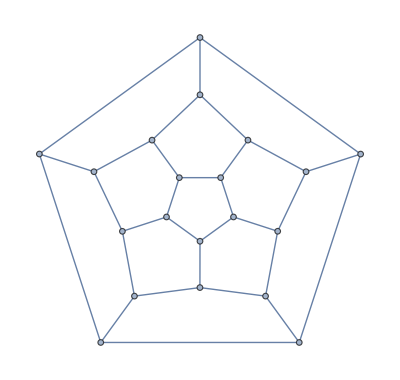

{{15<->1,1<->14,14<->9,9<->10,10<->18,18<->13,13<->17,17<->19,19<->3,3<->7,7<->16,16<->8,8<->12,12<->11,11<->5,5<->2,2<->6,6<->20,20<->4,4<->15},{15<->1,1<->14,14<->3,3<->7,7<->16,16<->8,8<->12,12<->11,11<->5,5<->19,19<->17,17<->9,9<->10,10<->18,18<->13,13<->2,2<->6,6<->20,20<->4,4<->15},{15<->1,1<->14,14<->3,3<->19,19<->5,5<->11,11<->7,7<->16,16<->8,8<->12,12<->6,6<->2,2<->13,13<->17,17<->9,9<->10,10<->18,18<->20,20<->4,4<->15},{15<->1,1<->14,14<->3,3<->19,19<->17,17<->9,9<->10,10<->18,18<->13,13<->2,2<->5,5<->11,11<->7,7<->16,16<->8,8<->12,12<->6,6<->20,20<->4,4<->15},{8<->16,16<->7,7<->11,11<->12,12<->6,6<->20,20<->18,18<->10,10<->9,9<->17,17<->13,13<->2,2<->5,5<->19,19<->3,3<->14,14<->1,1<->15,15<->4,4<->8},{8<->16,16<->7,7<->11,11<->12,12<->6,6<->2,2<->5,5<->19,19<->3,3<->14,14<->1,1<->15,15<->10,10<->9,9<->17,17<->13,13<->18,18<->20,20<->4,4<->8},{8<->16,16<->7,7<->3,3<->19,19<->17,17<->13,13<->2,2<->5,5<->11,11<->12,12<->6,6<->20,20<->18,18<->10,10<->9,9<->14,14<->1,1<->15,15<->4,4<->8},{8<->16,16<->7,7<->3,3<->19,19<->17,17<->9,9<->14,14<->1,1<->15,15<->10,10<->18,18<->13,13<->2,2<->5,5<->11,11<->12,12<->6,6<->20,20<->4,4<->8},{8<->16,16<->7,7<->3,3<->19,19<->5,5<->11,11<->12,12<->6,6<->2,2<->13,13<->17,17<->9,9<->14,14<->1,1<->15,15<->10,10<->18,18<->20,20<->4,4<->8},{8<->16,16<->7,7<->3,3<->14,14<->1,1<->15,15<->10,10<->9,9<->17,17<->19,19<->5,5<->11,11<->12,12<->6,6<->2,2<->13,13<->18,18<->20,20<->4,4<->8},{1<->14,14<->3,3<->7,7<->11,11<->5,5<->19,19<->17,17<->9,9<->10,10<->15,15<->4,4<->20,20<->18,18<->13,13<->2,2<->6,6<->12,12<->8,8<->16,16<->1},{1<->14,14<->3,3<->7,7<->11,11<->12,12<->6,6<->20,20<->18,18<->13,13<->2,2<->5,5<->19,19<->17,17<->9,9<->10,10<->15,15<->4,4<->8,8<->16,16<->1},{1<->14,14<->3,3<->19,19<->5,5<->2,2<->6,6<->20,20<->18,18<->13,13<->17,17<->9,9<->10,10<->15,15<->4,4<->8,8<->12,12<->11,11<->7,7<->16,16<->1},{1<->14,14<->3,3<->19,19<->17,17<->9,9<->10,10<->15,15<->4,4<->8,8<->12,12<->6,6<->20,20<->18,18<->13,13<->2,2<->5,5<->11,11<->7,7<->16,16<->1},{1<->14,14<->9,9<->10,10<->15,15<->4,4<->20,20<->18,18<->13,13<->17,17<->19,19<->3,3<->7,7<->11,11<->5,5<->2,2<->6,6<->12,12<->8,8<->16,16<->1},{1<->14,14<->9,9<->10,10<->15,15<->4,4<->8,8<->12,12<->11,11<->5,5<->2,2<->6,6<->20,20<->18,18<->13,13<->17,17<->19,19<->3,3<->7,7<->16,16<->1},{1<->14,14<->9,9<->17,17<->13,13<->2,2<->5,5<->19,19<->3,3<->7,7<->11,11<->12,12<->6,6<->20,20<->18,18<->10,10<->15,15<->4,4<->8,8<->16,16<->1},{1<->14,14<->9,9<->17,17<->13,13<->2,2<->6,6<->20,20<->18,18<->10,10<->15,15<->4,4<->8,8<->12,12<->11,11<->5,5<->19,19<->3,3<->7,7<->16,16<->1},{1<->14,14<->9,9<->17,17<->13,13<->18,18<->10,10<->15,15<->4,4<->20,20<->6,6<->2,2<->5,5<->19,19<->3,3<->7,7<->11,11<->12,12<->8,8<->16,16<->1},{1<->14,14<->9,9<->17,17<->19,19<->3,3<->7,7<->11,11<->5,5<->2,2<->13,13<->18,18<->10,10<->15,15<->4,4<->20,20<->6,6<->12,12<->8,8<->16,16<->1},{1<->15,15<->4,4<->20,20<->6,6<->2,2<->5,5<->19,19<->17,17<->13,13<->18,18<->10,10<->9,9<->14,14<->3,3<->7,7<->11,11<->12,12<->8,8<->16,16<->1},{1<->15,15<->4,4<->20,20<->18,18<->10,10<->9,9<->14,14<->3,3<->7,7<->11,11<->5,5<->19,19<->17,17<->13,13<->2,2<->6,6<->12,12<->8,8<->16,16<->1},{1<->15,15<->4,4<->8,8<->12,12<->11,11<->5,5<->19,19<->17,17<->13,13<->2,2<->6,6<->20,20<->18,18<->10,10<->9,9<->14,14<->3,3<->7,7<->16,16<->1},{1<->15,15<->4,4<->8,8<->12,12<->6,6<->20,20<->18,18<->10,10<->9,9<->14,14<->3,3<->19,19<->17,17<->13,13<->2,2<->5,5<->11,11<->7,7<->16,16<->1},{1<->15,15<->10,10<->9,9<->14,14<->3,3<->7,7<->11,11<->12,12<->6,6<->2,2<->5,5<->19,19<->17,17<->13,13<->18,18<->20,20<->4,4<->8,8<->16,16<->1},{1<->15,15<->10,10<->9,9<->14,14<->3,3<->19,19<->17,17<->13,13<->18,18<->20,20<->4,4<->8,8<->12,12<->6,6<->2,2<->5,5<->11,11<->7,7<->16,16<->1},{1<->15,15<->10,10<->18,18<->13,13<->2,2<->5,5<->19,19<->17,17<->9,9<->14,14<->3,3<->7,7<->11,11<->12,12<->6,6<->20,20<->4,4<->8,8<->16,16<->1},{1<->15,15<->10,10<->18,18<->13,13<->2,2<->6,6<->20,20<->4,4<->8,8<->12,12<->11,11<->5,5<->19,19<->17,17<->9,9<->14,14<->3,3<->7,7<->16,16<->1},{1<->15,15<->10,10<->18,18<->13,13<->17,17<->9,9<->14,14<->3,3<->19,19<->5,5<->2,2<->6,6<->20,20<->4,4<->8,8<->12,12<->11,11<->7,7<->16,16<->1},{1<->15,15<->10,10<->18,18<->20,20<->4,4<->8,8<->12,12<->6,6<->2,2<->13,13<->17,17<->9,9<->14,14<->3,3<->19,19<->5,5<->11,11<->7,7<->16,16<->1}}

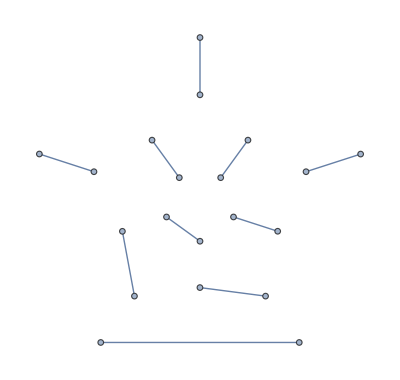
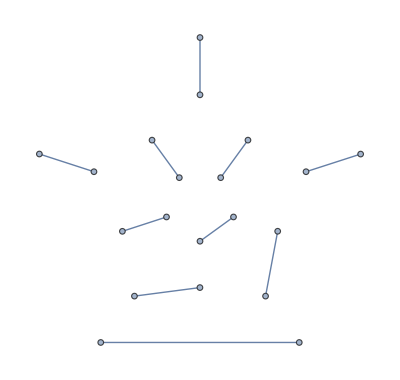
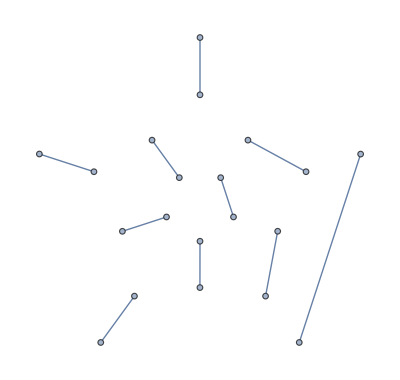
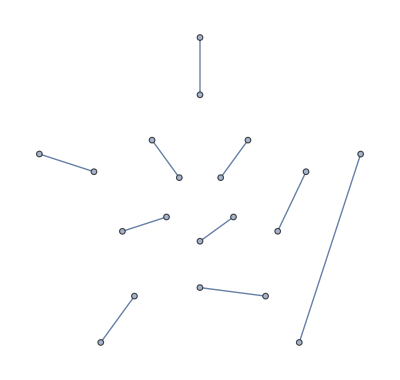
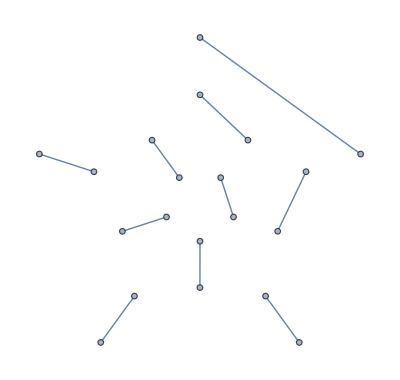
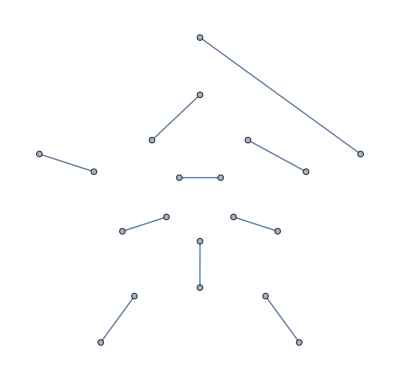
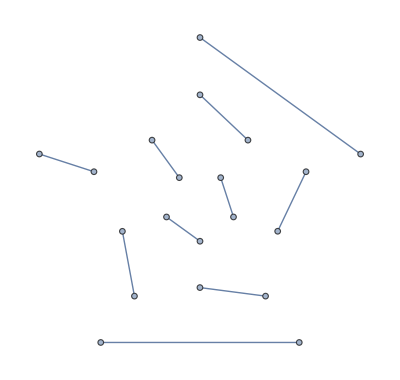
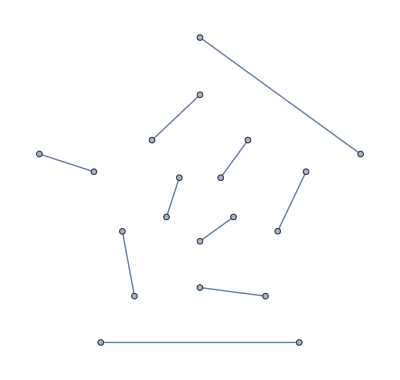

```mathematica
gh=PolyhedronData["Dodecahedron","SkeletonGraph"]
FindCycle[gh,{VertexCount[gh]},All]
Map[Style[HighlightGraph[gh,Map[Style[#,White,Background->Black]&,#]],Background->Black]&,%]
```

```mathematica
FullSimplify[(c-k(n-1))k+∑_(a=2)^(k-1) n a]
```

k (c+k)-1/2 (2+k+k^2) n

```mathematica
Expand[%]
```

c k+k^2-n-(k n)/2-(k^2 n)/2

```mathematica
FullSimplify[(k (k+c)-n(k^2+k+2)/2)/n]
```

(k (c+k)-1/2 (2+k+k^2) n)/n

```mathematica
(2 k (c+k)-(2+k+k^2) n)/(2n)
```

```mathematica
FullSimplify[(2 k (c+k)-(2+k+k^2) n)/(2 n),{n>0,k>0,Element[n,Integers],Element[k,Integers]}]
```

(2 k (c+k)-(2+k+k^2) n)/(2 n)